# Gubser semi-analytic solution Conserved Charge

## Deriving differential equations

```mathematica
a=1/3;
e[ρ_]:=α (T hat[ρ])^4 Cosh[(μ hat[ρ])/(T hat[ρ])];
p[ρ_]:=a e[ρ];
n[ρ_]:=a α (T hat[ρ])^3 Sinh[(μ hat[ρ])/(T hat[ρ])];
s[ρ_]:=a α (T hat[ρ])^2(4T hat[ρ]Cosh[(μ hat[ρ])/(T hat[ρ])]-μ hat[ρ]Sinh[(μ hat[ρ])/(T hat[ρ])]);
```

```mathematica
sol=Solve[{(1/(e[ρ]+p[ρ])(D[e[ρ],ρ]+2(e[ρ]+p[ρ])Tanh[ρ])//FullSimplify)==0,
(1/(e[ρ]+p[ρ])(D[n[ρ],ρ]+2n[ρ]Tanh[ρ])//FullSimplify)==0},{T hat'[ρ], μ hat'[ρ]}];
ConservEqs=(%/.Rule->Equal//FullSimplify)[[1]]
```

{T hat'[ρ]==-2/3 Tanh[ρ] T hat[ρ],μ hat'[ρ]==-2/3 Tanh[ρ] μ hat[ρ]}

## Constants

```mathematica
Clear[ℏc,ηOverS,α,c,sols,ρ,T]
```

```mathematica
ℏc=(197.326980/1000); 
ηOverS=0.2;
α=3 π^2/90(2(Nc^2-1)+7/2 Nc Nf)/.{Nc->3,Nf->2.5};
c=5;
```

## Solving differential equations

```mathematica
sols=NDSolve[{
ConservEqs[[1]],
ConservEqs[[2]],
T hat[0]==1.2 (*0.31532/ℏc*),
μ hat[0]==1.2 (*0.162056/ℏc *)},
{T hat,μ hat},
{ρ,-20,20}
];
```

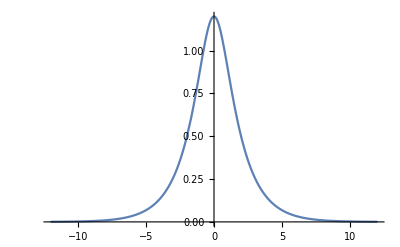

-Graphics-

```mathematica
(*μ hat[0] == 1.2*)
Plot[T hat[ρ]/.sols,{ρ,-12,12}]
Plot[μ hat[ρ]/.sols,{ρ,-12,12}]
```

```mathematica
(* μ hat[0] == 0.0*)
Plot[T hat[ρ]/.sols,{ρ,-12,12}]
Plot[μ hat[ρ]/.sols,{ρ,-12,12}]
```

-Graphics-

-Graphics-

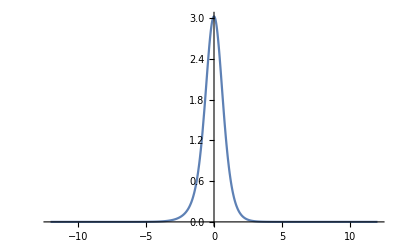

```mathematica
Plot[ℏc (T hat[ρ])^4 Cosh[(μ hat[ρ])/(T hat[ρ])]/.sols,{ρ,-12,12}, PlotRange->Full]
```

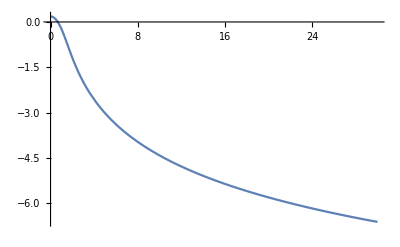

```mathematica
Plot[ArcSinh[-(1-τ^2+r^2)/(2 τ)]/.τ->1.2,{r, 0, 30}, PlotRange->All]
```

## Change of coordinates of solutions

```mathematica
ρ[τ_,r_]:=ArcSinh[-(1-τ^2+r^2)/(2τ)];
T[τ_,r_]:=ℏc((T hat[ρ[τ,r]]/.sols)/τ)[[1]];
μ[τ_,r_]:=ℏc((μ hat[ρ[τ,r]]/.sols)/τ)[[1]];
T[τ_,x_,y_]:= T[τ,√(x^2+y^2)];
μ[τ_,x_,y_]:= μ[τ,√(x^2+y^2)];
u r[τ_,r_]:=Sinh[ArcTanh[(2τ r)/(1+τ^2+r^2)]];
u x[τ_,x_,y_]:=Piecewise[{{x/(√(x^2+y^2))Sinh[ArcTanh[(2τ √(x^2+y^2))/(1+τ^2+x^2+y^2)]],√(x^2+y^2)≠0},{0.0,√(x^2+y^2)==0}}];
u y[τ_,x_,y_]:=Piecewise[{{y/(√(x^2+y^2))Sinh[ArcTanh[(2τ √(x^2+y^2))/(1+τ^2+x^2+y^2)]],√(x^2+y^2)≠0},{0.0,√(x^2+y^2)==0}}];
```

## Plots

### Plot drawing

```mathematica
(* τ's that will be plotted *)
times={1.2,2,3};

plotGrid=GraphicsGrid[
{
{
Plot[Evaluate@Table[T[τ,x,y]/.{τ->times[[i]],y->0},{i,1,Length@times}],{x,-6,6},
PlotRange->{{-6,6},(*{0.04,0.25}*)Automatic},
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","T [GeV]"},PlotTheme->"Monochrome",PlotStyle->Gray,
Axes->False,PlotLabels->Placed[Table[StringJoin[{"τ=",ToString[times[[i]]]," fm"}],{i,1,Length@times}],Table[{Scaled[0.5],Above},{i,1,Length@times}]]],

Plot[Evaluate@Table[μ[τ,x,y]/.{τ->times[[i]],y->0},{i,1,Length@times}],{x,-6,6},
PlotRange->Automatic,
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","μ [GeV]"},PlotTheme->"Monochrome",PlotStyle->Gray,
Axes->False],
Plot[Evaluate@Table[u x[τ,x,y]/.{τ->times[[i]],y->0},{i,1,Length@times}],{x,-6,6},
PlotRange->{{-6,6},{-3,3}},
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","u^x"},PlotTheme->"Monochrome",PlotStyle->Gray,
Axes->False]
}
},ImageSize->128*6];
```

### Display plots

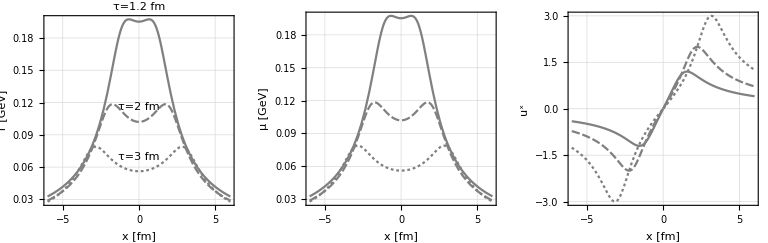

```mathematica
(*μ hat[0] == 1.2, ϕ=0.0*)
plotGrid
```

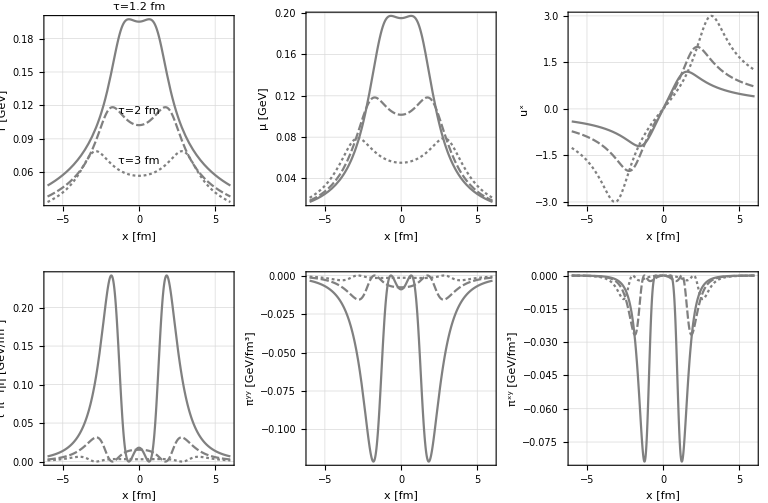

```mathematica
(*μ hat[0] == 1.2, ϕ≠0.0*)
plotGrid
```

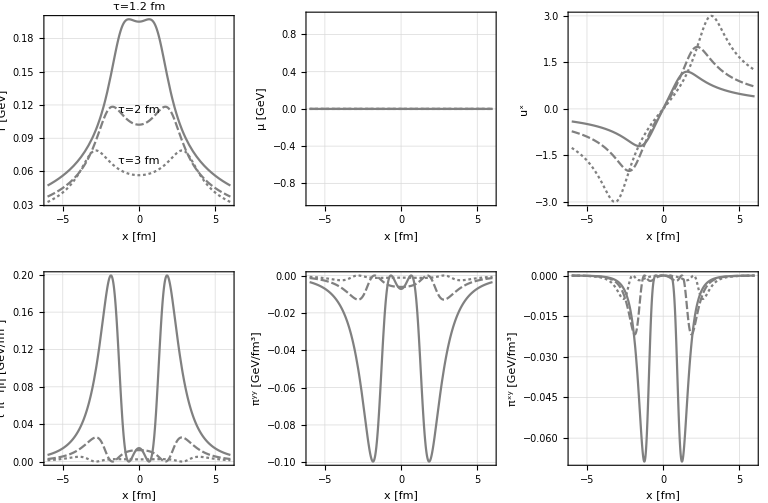

```mathematica
(*μ hat[0] == 0.0*)
plotGrid
```

## Output table

### Modules to write output files

```mathematica
(* Table with columns "x [fm], y [fm], T [GeV], u^x, u^y, π^xx [GeV/fm^3], π^yy [GeV/fm^3], π^xy [GeV/fm^3], τ^2π^ηη [GeV/fm^3]" as a function of time τ *)
```

```mathematica
formatted InitialProfile Table[τ_:1,gridMax_:5,gridStep_:0.05,path_:NotebookDirectory[]]:=
Module[
{xMax=Abs@gridMax,
xMin=-Abs@gridMax,
yMax=Abs@gridMax,
yMin=-Abs@gridMax,
Δx=Abs@gridStep,
Δy=Abs@gridStep},
outputTable=ArrayFlatten[
Table[{
DecimalForm@N[x,7],
DecimalForm@N[y,7],
DecimalForm@N[T[Τ,x,y],7],
DecimalForm@N[u x[Τ,x,y],7],
DecimalForm@N[u y[Τ,x,y],7],
DecimalForm@N[π xx[Τ,x,y],7],
DecimalForm@N[π yy[Τ,x,y],7],
DecimalForm@N[π xy[Τ,x,y],7],
DecimalForm@N[(Τ^2 π ηη[Τ,x,y]),7]
}/.{Τ->τ},
{x,xMin,xMax,Δx},{y,yMin,yMax,Δy}],1];
format[x_]:=ToString@NumberForm[x,{7,6},NumberFormat->(StringJoin[{#1,""}/. "":>""/;#2==""]&)];
formattedOutput=Map[format,outputTable,{2}];
filename="Initial_Profile_tau="<>ToString[τ]<>"fm.dat";
completePath=FileNameJoin[{path,filename}];
Export[completePath,formattedOutput,"Table","FieldSeparators"->"     "];
];
formatted yeq0 Table[τ_:1,gridMax_:5,gridStep_:0.05,path_:NotebookDirectory[]]:=
Module[
{xMax=Abs@gridMax,
xMin=-Abs@gridMax,
Δx=Abs@gridStep},
outputTable=ArrayFlatten[
Table[{
DecimalForm@N[x,7],
DecimalForm@N[y,7],
DecimalForm@N[T[Τ,x,y],7],
DecimalForm@N[u x[Τ,x,y],7],
DecimalForm@N[u y[Τ,x,y],7],
DecimalForm@N[π xx[Τ,x,y],7],
DecimalForm@N[π yy[Τ,x,y],7],
DecimalForm@N[π xy[Τ,x,y],7],
DecimalForm@N[(Τ^2 π ηη[Τ,x,y]),7]
}/.{Τ->τ,y->0},
{x,xMin,xMax,Δx}],0];
format[x_]:=ToString@NumberForm[x,{7,6},NumberFormat->(StringJoin[{#1,""}/. "":>""/;#2==""]&)];
formattedOutput=Map[format,outputTable,{2}];
filename="y=0_tau="<>ToString[τ]<>"_SemiAnalytic.dat";
completePath=FileNameJoin[{path,filename}];
Export[completePath,formattedOutput,"Table","FieldSeparators"->"     "];
];
formatted yeqx Table[τ_:1,gridMax_:5,gridStep_:0.05,path_:NotebookDirectory[]]:=
Module[
{xMax=Abs@gridMax,
xMin=-Abs@gridMax,
Δx=Abs@gridStep},
outputTable=ArrayFlatten[
Table[{
DecimalForm@N[x,7],
DecimalForm@N[y,7],
DecimalForm@N[T[Τ,x,y],7],
DecimalForm@N[u x[Τ,x,y],7],
DecimalForm@N[u y[Τ,x,y],7],
DecimalForm@N[π xx[Τ,x,y],7],
DecimalForm@N[π yy[Τ,x,y],7],
DecimalForm@N[π xy[Τ,x,y],7],
DecimalForm@N[(Τ^2 π ηη[Τ,x,y]),7]
}/.{Τ->τ,y->x},
{x,xMin,xMax,Δx}],0];
format[x_]:=ToString@NumberForm[x,{7,6},NumberFormat->(StringJoin[{#1,""}/. "":>""/;#2==""]&)];
formattedOutput=Map[format,outputTable,{2}];
filename="y=x_tau="<>ToString[τ]<>"_SemiAnalytic.dat";
completePath=FileNameJoin[{path,filename}];
Export[completePath,formattedOutput,"Table","FieldSeparators"->"     "];
]
```

### Call module

```mathematica
formatted InitialProfile Table[1,6,0.05]
```

```mathematica
formatted yeq0 Table[1,5,0.05]
```

```mathematica
formatted yeqx Table[2.3,5,0.05]
```

## Output for initial conditions of GReX

```mathematica
Table[{x,ℏc^4 e[x]/.sols[[1]],ℏc^3 n[x]/.sols[[1]]},{x,-20, 20, 0.1}]
Export["/home/ominusliticus/Documents/Research/PostDoc/Code/GReX/Problems/Gubser_Test_Ideal/initial_conditions_ideal.tsv",%]
```

{{-20.,3.82971×10^-22,3.15226×10^-17},{-19.9,5.00028×10^-22,3.85029×10^-17},{-19.8,6.52947×10^-22,4.70334×10^-17},{-19.7,8.52751×10^-22,5.74598×10^-17},{-19.6,1.11378×10^-21,7.02014×10^-17},{-19.5,1.45463×10^-21,8.57653×10^-17},{-19.4,1.8994×10^-21,1.04764×10^-16},{-19.3,2.47964×10^-21,1.2795×10^-16},{-19.2,3.23708×10^-21,1.56265×10^-16},{-19.1,4.22626×10^-21,1.9086×10^-16},{-19.,5.51822×10^-21,2.33129×10^-16},{-18.9,7.20535×10^-21,2.84766×10^-16},{-18.8,9.40743×10^-21,3.47817×10^-16},{-18.7,1.22815×10^-20,4.248×10^-16},{-18.6,1.60342×10^-20,5.18839×10^-16},{-18.5,2.09352×10^-20,6.33731×10^-16},{-18.4,2.73351×10^-20,7.74084×10^-16},{-18.3,3.56886×10^-20,9.45464×10^-16},{-18.2,4.65916×10^-20,1.15472×10^-15},{-18.1,6.08283×10^-20,1.41035×10^-15},{-18.,7.94216×10^-20,1.72267×10^-15},{-17.9,1.03701×10^-19,2.10419×10^-15},{-17.8,1.35392×10^-19,2.57006×10^-15},{-17.7,1.76757×10^-19,3.13892×10^-15},{-17.6,2.30772×10^-19,3.83385×10^-15},{-17.5,3.01314×10^-19,4.68287×10^-15},{-17.4,3.93425×10^-19,5.71997×10^-15},{-17.3,5.13641×10^-19,6.98621×10^-15},{-17.2,6.70544×10^-19,8.53234×10^-15},{-17.1,8.7542×10^-19,1.0421×10^-14},{-17.,1.14297×10^-18,1.27284×10^-14},{-16.9,1.49232×10^-18,1.55469×10^-14},{-16.8,1.94827×10^-18,1.89882×10^-14},{-16.7,2.54344×10^-18,2.31907×10^-14},{-16.6,3.32062×10^-18,2.83245×10^-14},{-16.5,4.33559×10^-18,3.45966×10^-14},{-16.4,5.66081×10^-18,4.22578×10^-14},{-16.3,7.39045×10^-18,5.1612×10^-14},{-16.2,9.64848×10^-18,6.30364×10^-14},{-16.1,1.25973×10^-17,7.69937×10^-14},{-16.,1.64483×10^-17,9.40455×10^-14},{-15.9,2.14762×10^-17,1.14872×10^-13},{-15.8,2.80388×10^-17,1.40303×10^-13},{-15.7,3.6607×10^-17,1.71364×10^-13},{-15.6,4.77954×10^-17,2.09309×10^-13},{-15.5,6.24029×10^-17,2.55653×10^-13},{-15.4,8.14711×10^-17,3.12248×10^-13},{-15.3,1.06369×10^-16,3.8138×10^-13},{-15.2,1.38879×10^-16,4.65828×10^-13},{-15.1,1.81322×10^-16,5.68965×10^-13},{-15.,2.36728×10^-16,6.9492×10^-13},{-14.9,3.09075×10^-16,8.4878×10^-13},{-14.8,4.03542×10^-16,1.03673×10^-12},{-14.7,5.26859×10^-16,1.26625×10^-12},{-14.6,6.87854×10^-16,1.54657×10^-12},{-14.5,8.9808×10^-16,1.88901×10^-12},{-14.4,1.17257×10^-15,2.30728×10^-12},{-14.3,1.53087×10^-15,2.81807×10^-12},{-14.2,1.99869×10^-15,3.44196×10^-12},{-14.1,2.60956×10^-15,4.20409×10^-12},{-14.,3.4071×10^-15,5.13495×10^-12},{-13.9,4.4482×10^-15,6.2717×10^-12},{-13.8,5.80756×10^-15,7.66025×10^-12},{-13.7,7.5826×10^-15,9.35645×10^-12},{-13.6,9.8999×10^-15,1.1428×10^-11},{-13.5,1.2925×10^-14,1.39579×10^-11},{-13.4,1.6875×10^-14,1.70483×10^-11},{-13.3,2.20328×10^-14,2.08233×10^-11},{-13.2,2.87658×10^-14,2.54334×10^-11},{-13.1,3.75561×10^-14,3.1064×10^-11},{-13.,4.90342×10^-14,3.79421×10^-11},{-12.9,6.40205×10^-14,4.63432×10^-11},{-12.8,8.35834×10^-14,5.66027×10^-11},{-12.7,1.09126×10^-13,6.91345×10^-11},{-12.6,1.4248×10^-13,8.44426×10^-11},{-12.5,1.86022×10^-13,1.03138×10^-10},{-12.4,2.42865×10^-13,1.25971×10^-10},{-12.3,3.17089×10^-13,1.53863×10^-10},{-12.2,4.14003×10^-13,1.87932×10^-10},{-12.1,5.40513×10^-13,2.29537×10^-10},{-12.,7.05689×10^-13,2.80354×10^-10},{-11.9,9.21372×10^-13,3.42431×10^-10},{-11.8,1.20296×10^-12,4.18249×10^-10},{-11.7,1.57055×10^-12,5.10841×10^-10},{-11.6,2.05052×10^-12,6.23945×10^-10},{-11.5,2.67725×10^-12,7.62103×10^-10},{-11.4,3.49538×10^-12,9.30825×10^-10},{-11.3,4.5635×10^-12,1.1369×10^-9},{-11.2,5.95824×10^-12,1.38863×10^-9},{-11.1,7.77922×10^-12,1.69609×10^-9},{-11.,1.01563×10^-11,2.07157×10^-9},{-10.9,1.32601×10^-11,2.53022×10^-9},{-10.8,1.73129×10^-11,3.09047×10^-9},{-10.7,2.26038×10^-11,3.7747×10^-9},{-10.6,2.95113×10^-11,4.6104×10^-9},{-10.5,3.85306×10^-11,5.63121×10^-9},{-10.4,5.03056×10^-11,6.87796×10^-9},{-10.3,6.56786×10^-11,8.4007×10^-9},{-10.2,8.57514×10^-11,1.02607×10^-8},{-10.1,1.11957×10^-10,1.25325×10^-8},{-10.,1.4617×10^-10,1.53071×10^-8},{-9.9,1.90843×10^-10,1.86963×10^-8},{-9.8,2.49165×10^-10,2.28356×10^-8},{-9.7,3.25308×10^-10,2.78913×10^-8},{-9.6,4.24729×10^-10,3.40668×10^-8},{-9.5,5.54527×10^-10,4.16092×10^-8},{-9.4,7.23987×10^-10,5.08212×10^-8},{-9.3,9.45253×10^-10,6.20738×10^-8},{-9.2,1.23412×10^-9,7.58169×10^-8},{-9.1,1.61126×10^-9,9.26023×10^-8},{-9.,2.1037×10^-9,1.13106×10^-7},{-8.9,2.74659×10^-9,1.38147×10^-7},{-8.8,3.58593×10^-9,1.68732×10^-7},{-8.7,4.68187×10^-9,2.06092×10^-7},{-8.6,6.11265×10^-9,2.51721×10^-7},{-8.5,7.98063×10^-9,3.07451×10^-7},{-8.4,1.04197×10^-8,3.75525×10^-7},{-8.3,1.36039×10^-8,4.58666×10^-7},{-8.2,1.77612×10^-8,5.60211×10^-7},{-8.1,2.31894×10^-8,6.8425×10^-7},{-8.,3.02761×10^-8,8.35743×10^-7},{-7.9,3.95283×10^-8,1.02077×10^-6},{-7.8,5.1609×10^-8,1.24678×10^-6},{-7.7,6.73807×10^-8,1.52282×10^-6},{-7.6,8.79718×10^-8,1.85997×10^-6},{-7.5,1.14858×10^-7,2.27179×10^-6},{-7.4,1.49959×10^-7,2.77476×10^-6},{-7.3,1.95785×10^-7,3.38908×10^-6},{-7.2,2.55621×10^-7,4.13947×10^-6},{-7.1,3.33739×10^-7,5.05594×10^-6},{-7.,4.35726×10^-7,6.1753×10^-6},{-6.9,5.68894×10^-7,7.5426×10^-6},{-6.8,7.42748×10^-7,9.21252×10^-6},{-6.7,9.69725×10^-7,0.0000112521},{-6.6,1.26609×10^-6,0.0000137435},{-6.5,1.65301×10^-6,0.0000167863},{-6.4,2.15815×10^-6,0.0000205026},{-6.3,2.81773×10^-6,0.0000250422},{-6.2,3.67882×10^-6,0.0000305864},{-6.1,4.80303×10^-6,0.000037358},{-6.,6.27093×10^-6,0.0000456296},{-5.9,8.18733×10^-6,0.000055732},{-5.8,0.0000106894,0.000068071},{-5.7,0.000013956,0.0000831417},{-5.6,0.000018221,0.000101549},{-5.5,0.0000237892,0.000124032},{-5.4,0.000031059,0.000151491},{-5.3,0.0000405503,0.00018503},{-5.2,0.0000529418,0.000225994},{-5.1,0.00006912,0.000276026},{-5.,0.0000902413,0.000337133},{-4.9,0.000117817,0.000411768},{-4.8,0.000153817,0.000502921},{-4.7,0.000200816,0.000614252},{-4.6,0.000262173,0.00075022},{-4.5,0.000342275,0.000916281},{-4.4,0.000446844,0.00111909},{-4.3,0.000583349,0.00136677},{-4.2,0.000761541,0.00166923},{-4.1,0.000994141,0.00203861},{-4.,0.00129774,0.00248966},{-3.9,0.00169401,0.00304042},{-3.8,0.00221117,0.0037129},{-3.7,0.00288606,0.00453395},{-3.6,0.0037667,0.00553628},{-3.5,0.00491565,0.00675979},{-3.4,0.00641445,0.0082531},{-3.3,0.00836924,0.0100754},{-3.2,0.0109182,0.0122987},{-3.1,0.0142409,0.0150107},{-3.,0.0185707,0.0183176},{-2.9,0.0242107,0.0223487},{-2.8,0.0315533,0.0272603},{-2.7,0.0411067,0.0332416},{-2.6,0.0535269,0.0405207},{-2.5,0.0696592,0.049372},{-2.4,0.090589,0.0601248},{-2.3,0.117705,0.0731719},{-2.2,0.152777,0.0889798},{-2.1,0.198046,0.108099},{-2.,0.256327,0.131173},{-1.9,0.331134,0.158946},{-1.8,0.426795,0.19227},{-1.7,0.548569,0.232098},{-1.6,0.702735,0.279474},{-1.5,0.896612,0.335506},{-1.4,1.13846,0.401316},{-1.3,1.43723,0.47796},{-1.2,1.80195,0.566311},{-1.1,2.2409,0.666906},{-1.,2.76017,0.779739},{-0.9,3.36186,0.904028},{-0.8,4.04183,1.03796},{-0.7,4.7874,1.17848},{-0.6,5.5753,1.32114},{-0.5,6.37087,1.46015},{-0.4,7.12896,1.58861},{-0.3,7.79747,1.69907},{-0.2,8.3233,1.78431},{-0.1,8.66013,1.83819},{0.,8.77618,1.85663},{0.1,8.66013,1.83819},{0.2,8.3233,1.78431},{0.3,7.79747,1.69907},{0.4,7.12896,1.58861},{0.5,6.37087,1.46015},{0.6,5.5753,1.32114},{0.7,4.7874,1.17848},{0.8,4.04183,1.03796},{0.9,3.36186,0.904028},{1.,2.76017,0.779739},{1.1,2.2409,0.666906},{1.2,1.80195,0.566311},{1.3,1.43723,0.47796},{1.4,1.13846,0.401316},{1.5,0.896612,0.335506},{1.6,0.702735,0.279474},{1.7,0.548569,0.232098},{1.8,0.426795,0.19227},{1.9,0.331134,0.158946},{2.,0.256327,0.131173},{2.1,0.198046,0.108099},{2.2,0.152777,0.0889798},{2.3,0.117705,0.0731719},{2.4,0.090589,0.0601248},{2.5,0.0696592,0.049372},{2.6,0.0535269,0.0405207},{2.7,0.0411067,0.0332416},{2.8,0.0315533,0.0272603},{2.9,0.0242107,0.0223487},{3.,0.0185707,0.0183176},{3.1,0.0142409,0.0150107},{3.2,0.0109182,0.0122987},{3.3,0.00836924,0.0100754},{3.4,0.00641445,0.0082531},{3.5,0.00491565,0.00675979},{3.6,0.0037667,0.00553628},{3.7,0.00288606,0.00453395},{3.8,0.00221117,0.0037129},{3.9,0.00169401,0.00304042},{4.,0.00129774,0.00248966},{4.1,0.000994141,0.00203861},{4.2,0.000761541,0.00166923},{4.3,0.000583349,0.00136677},{4.4,0.000446844,0.00111909},{4.5,0.000342275,0.000916281},{4.6,0.000262173,0.00075022},{4.7,0.000200816,0.000614252},{4.8,0.000153817,0.000502921},{4.9,0.000117817,0.000411768},{5.,0.0000902413,0.000337133},{5.1,0.00006912,0.000276026},{5.2,0.0000529418,0.000225994},{5.3,0.0000405503,0.00018503},{5.4,0.000031059,0.000151491},{5.5,0.0000237892,0.000124032},{5.6,0.000018221,0.000101549},{5.7,0.000013956,0.0000831417},{5.8,0.0000106894,0.000068071},{5.9,8.18733×10^-6,0.000055732},{6.,6.27093×10^-6,0.0000456296},{6.1,4.80303×10^-6,0.000037358},{6.2,3.67882×10^-6,0.0000305864},{6.3,2.81773×10^-6,0.0000250422},{6.4,2.15815×10^-6,0.0000205026},{6.5,1.65301×10^-6,0.0000167863},{6.6,1.26609×10^-6,0.0000137435},{6.7,9.69725×10^-7,0.0000112521},{6.8,7.42748×10^-7,9.21252×10^-6},{6.9,5.68894×10^-7,7.5426×10^-6},{7.,4.35726×10^-7,6.1753×10^-6},{7.1,3.33739×10^-7,5.05594×10^-6},{7.2,2.55621×10^-7,4.13947×10^-6},{7.3,1.95785×10^-7,3.38908×10^-6},{7.4,1.49959×10^-7,2.77476×10^-6},{7.5,1.14858×10^-7,2.27179×10^-6},{7.6,8.79718×10^-8,1.85997×10^-6},{7.7,6.73807×10^-8,1.52282×10^-6},{7.8,5.1609×10^-8,1.24678×10^-6},{7.9,3.95283×10^-8,1.02077×10^-6},{8.,3.02761×10^-8,8.35743×10^-7},{8.1,2.31894×10^-8,6.8425×10^-7},{8.2,1.77612×10^-8,5.60211×10^-7},{8.3,1.36039×10^-8,4.58666×10^-7},{8.4,1.04197×10^-8,3.75525×10^-7},{8.5,7.98063×10^-9,3.07451×10^-7},{8.6,6.11265×10^-9,2.51721×10^-7},{8.7,4.68187×10^-9,2.06092×10^-7},{8.8,3.58593×10^-9,1.68732×10^-7},{8.9,2.74659×10^-9,1.38147×10^-7},{9.,2.1037×10^-9,1.13106×10^-7},{9.1,1.61126×10^-9,9.26023×10^-8},{9.2,1.23412×10^-9,7.58169×10^-8},{9.3,9.45253×10^-10,6.20738×10^-8},{9.4,7.23987×10^-10,5.08212×10^-8},{9.5,5.54527×10^-10,4.16092×10^-8},{9.6,4.24729×10^-10,3.40668×10^-8},{9.7,3.25308×10^-10,2.78913×10^-8},{9.8,2.49165×10^-10,2.28356×10^-8},{9.9,1.90843×10^-10,1.86963×10^-8},{10.,1.4617×10^-10,1.53071×10^-8},{10.1,1.11957×10^-10,1.25325×10^-8},{10.2,8.57514×10^-11,1.02607×10^-8},{10.3,6.56786×10^-11,8.4007×10^-9},{10.4,5.03056×10^-11,6.87796×10^-9},{10.5,3.85306×10^-11,5.63121×10^-9},{10.6,2.95113×10^-11,4.6104×10^-9},{10.7,2.26038×10^-11,3.7747×10^-9},{10.8,1.73129×10^-11,3.09047×10^-9},{10.9,1.32601×10^-11,2.53022×10^-9},{11.,1.01563×10^-11,2.07157×10^-9},{11.1,7.77922×10^-12,1.69609×10^-9},{11.2,5.95824×10^-12,1.38863×10^-9},{11.3,4.5635×10^-12,1.1369×10^-9},{11.4,3.49538×10^-12,9.30825×10^-10},{11.5,2.67725×10^-12,7.62103×10^-10},{11.6,2.05052×10^-12,6.23945×10^-10},{11.7,1.57055×10^-12,5.10841×10^-10},{11.8,1.20296×10^-12,4.18249×10^-10},{11.9,9.21372×10^-13,3.42431×10^-10},{12.,7.05689×10^-13,2.80354×10^-10},{12.1,5.40513×10^-13,2.29537×10^-10},{12.2,4.14003×10^-13,1.87932×10^-10},{12.3,3.17089×10^-13,1.53863×10^-10},{12.4,2.42865×10^-13,1.25971×10^-10},{12.5,1.86022×10^-13,1.03138×10^-10},{12.6,1.4248×10^-13,8.44426×10^-11},{12.7,1.09126×10^-13,6.91345×10^-11},{12.8,8.35834×10^-14,5.66027×10^-11},{12.9,6.40205×10^-14,4.63432×10^-11},{13.,4.90342×10^-14,3.79421×10^-11},{13.1,3.75561×10^-14,3.1064×10^-11},{13.2,2.87658×10^-14,2.54334×10^-11},{13.3,2.20328×10^-14,2.08233×10^-11},{13.4,1.6875×10^-14,1.70483×10^-11},{13.5,1.2925×10^-14,1.39579×10^-11},{13.6,9.8999×10^-15,1.1428×10^-11},{13.7,7.5826×10^-15,9.35645×10^-12},{13.8,5.80756×10^-15,7.66025×10^-12},{13.9,4.4482×10^-15,6.2717×10^-12},{14.,3.4071×10^-15,5.13495×10^-12},{14.1,2.60956×10^-15,4.20409×10^-12},{14.2,1.99869×10^-15,3.44196×10^-12},{14.3,1.53087×10^-15,2.81807×10^-12},{14.4,1.17257×10^-15,2.30728×10^-12},{14.5,8.9808×10^-16,1.88901×10^-12},{14.6,6.87854×10^-16,1.54657×10^-12},{14.7,5.26859×10^-16,1.26625×10^-12},{14.8,4.03542×10^-16,1.03673×10^-12},{14.9,3.09075×10^-16,8.4878×10^-13},{15.,2.36728×10^-16,6.9492×10^-13},{15.1,1.81322×10^-16,5.68965×10^-13},{15.2,1.38879×10^-16,4.65828×10^-13},{15.3,1.06369×10^-16,3.8138×10^-13},{15.4,8.14711×10^-17,3.12248×10^-13},{15.5,6.24029×10^-17,2.55653×10^-13},{15.6,4.77954×10^-17,2.09309×10^-13},{15.7,3.6607×10^-17,1.71364×10^-13},{15.8,2.80388×10^-17,1.40303×10^-13},{15.9,2.14762×10^-17,1.14872×10^-13},{16.,1.64483×10^-17,9.40455×10^-14},{16.1,1.25973×10^-17,7.69937×10^-14},{16.2,9.64848×10^-18,6.30364×10^-14},{16.3,7.39045×10^-18,5.1612×10^-14},{16.4,5.66081×10^-18,4.22578×10^-14},{16.5,4.33559×10^-18,3.45966×10^-14},{16.6,3.32062×10^-18,2.83245×10^-14},{16.7,2.54344×10^-18,2.31907×10^-14},{16.8,1.94827×10^-18,1.89882×10^-14},{16.9,1.49232×10^-18,1.55469×10^-14},{17.,1.14297×10^-18,1.27284×10^-14},{17.1,8.7542×10^-19,1.0421×10^-14},{17.2,6.70544×10^-19,8.53234×10^-15},{17.3,5.13641×10^-19,6.98621×10^-15},{17.4,3.93425×10^-19,5.71997×10^-15},{17.5,3.01314×10^-19,4.68287×10^-15},{17.6,2.30772×10^-19,3.83385×10^-15},{17.7,1.76757×10^-19,3.13892×10^-15},{17.8,1.35392×10^-19,2.57006×10^-15},{17.9,1.03701×10^-19,2.10419×10^-15},{18.,7.94216×10^-20,1.72267×10^-15},{18.1,6.08283×10^-20,1.41035×10^-15},{18.2,4.65916×10^-20,1.15472×10^-15},{18.3,3.56886×10^-20,9.45464×10^-16},{18.4,2.73351×10^-20,7.74084×10^-16},{18.5,2.09352×10^-20,6.33731×10^-16},{18.6,1.60342×10^-20,5.18839×10^-16},{18.7,1.22815×10^-20,4.248×10^-16},{18.8,9.40743×10^-21,3.47817×10^-16},{18.9,7.20535×10^-21,2.84766×10^-16},{19.,5.51822×10^-21,2.33129×10^-16},{19.1,4.22626×10^-21,1.9086×10^-16},{19.2,3.23708×10^-21,1.56265×10^-16},{19.3,2.47964×10^-21,1.2795×10^-16},{19.4,1.8994×10^-21,1.04764×10^-16},{19.5,1.45463×10^-21,8.57653×10^-17},{19.6,1.11378×10^-21,7.02014×10^-17},{19.7,8.52751×10^-22,5.74598×10^-17},{19.8,6.52947×10^-22,4.70334×10^-17},{19.9,5.00028×10^-22,3.85029×10^-17},{20.,3.82971×10^-22,3.15226×10^-17}}

/home/ominusliticus/Documents/Research/PostDoc/Code/GReX/Problems/Gubser_Test_Ideal/initial_conditions_ideal.tsv

```mathematica
NotebookDirectory[]"test.dat"
```

/home/ominusliticus/Documents/Research/PostDoc/Noronha-Hostler/DissipativeGubserWithMu/ test.dat

```mathematica
Length@Table[x,{x,-12, 12, 0.1}]
```

241

```mathematica
rho
4/3 α ℏc (((T hat[rho])^4 Cosh[(μ hat[rho])/(T hat[rho])]π bar ηη[rho])/.sols[[1]])
format[x_]:=ToString@NumberForm[x,{7,6},NumberFormat->(StringJoin[{#1,""}/. "":>""/;#2==""]&)];
Map[format,(4/3 α ℏc (((T hat[rho])^4 Cosh[(μ hat[rho])/(T hat[rho])]π bar ηη[rho])/.sols[[1]])),0]
```

-12.

4.36244×10^-10

```mathematica
TraditionalForm[4.36243925260463*^-10]
```

4.36244×10^-10

```mathematica
DSolve[{x'[t]+x[t]==-x[t]^2},x[t],t]
```

{{x[t]→-ⅇ^C[1]/(-ⅇ^t+ⅇ^C[1])}}

# Gubser semi-analytic solution Viscous and Conserved Charge

## Deriving differential equations

```mathematica
a=1/3;
e[ρ_]:=α (T hat[ρ])^4 Cosh[(μ hat[ρ])/(T hat[ρ])];
p[ρ_]:=a e[ρ];
n[ρ_]:=a α (T hat[ρ])^3 Sinh[(μ hat[ρ])/(T hat[ρ])];
s[ρ_]:=a α (T hat[ρ])^2(4T hat[ρ]Cosh[(μ hat[ρ])/(T hat[ρ])]-μ hat[ρ]Sinh[(μ hat[ρ])/(T hat[ρ])]);
```

```mathematica
D[e[ρ],ρ]//FullSimplify
```

α (T hat[ρ])^2 (4 Cosh[(μ hat[ρ])/(T hat[ρ])] T hat[ρ] T hat'[ρ]+Sinh[(μ hat[ρ])/(T hat[ρ])] (-μ hat[ρ] T hat'[ρ]+T hat[ρ] μ hat'[ρ]))

```mathematica
sol=Solve[{(1/(e[ρ]+p[ρ])(D[e[ρ],ρ]+2(e[ρ]+p[ρ])Tanh[ρ]-π bar ηη[ρ](e[ρ]+p[ρ])Tanh[ρ])//FullSimplify)==0,
(1/(e[ρ]+p[ρ])(D[n[ρ],ρ]+2n[ρ]Tanh[ρ])//FullSimplify)==0},{T hat'[ρ], μ hat'[ρ]}];
ConservEqs=(%/.Rule->Equal//FullSimplify)[[1]]
```

{T hat'[ρ]==2/3 Tanh[ρ] T hat[ρ] (-1+(2 π bar ηη[ρ])/(1+3 Sech[(μ hat[ρ])/(T hat[ρ])]^2)),μ hat'[ρ]==(2 Tanh[ρ] (μ hat[ρ] (1+3 Sech[(μ hat[ρ])/(T hat[ρ])]^2-2 π bar ηη[ρ])+6 Tanh[(μ hat[ρ])/(T hat[ρ])] T hat[ρ] π bar ηη[ρ]))/(-12+9 Tanh[(μ hat[ρ])/(T hat[ρ])]^2)}

```mathematica
D[π bar ηη[ρ],ρ]+(π bar ηη[ρ])/(e[ρ]+p[ρ])D[e[ρ]+p[ρ],ρ]+1/τR π bar ηη[ρ]-(4/(3c)Tanh[ρ]-8/3 π bar ηη[ρ]Tanh[ρ])-0/(35τR)(π bar ηη[ρ])^2 -0/21 π bar ηη[ρ]Tanh[ρ];
(%/.sol)[[1]]//FullSimplify
piEq=(%/.τR->c ηOverS s[ρ]/(e[ρ]+p[ρ]))==0
```

-(4 Tanh[ρ])/(3 c)+(π bar ηη[ρ])/τR+4/3 Tanh[ρ] (π bar ηη[ρ])^2+π bar ηη'[ρ]

-(4 Tanh[ρ])/(3 c)+(4 Cosh[(μ hat[ρ])/(T hat[ρ])] (T hat[ρ])^2 π bar ηη[ρ])/(c ηOverS (4 Cosh[(μ hat[ρ])/(T hat[ρ])] T hat[ρ]-Sinh[(μ hat[ρ])/(T hat[ρ])] μ hat[ρ]))+4/3 Tanh[ρ] (π bar ηη[ρ])^2+π bar ηη'[ρ]==0

## Constants

```mathematica
Clear[ℏc,ηOverS,α,c,sols,ρ,T]
```

```mathematica
ℏc=(197.326980/1000); 
ηOverS=0.2;
α=3 π^2/90(2(Nc^2-1)+7/2 Nc Nf)/.{Nc->3,Nf->2.5};
c=5;
```

## Solving differential equations

```mathematica
sols=NDSolve[{
ConservEqs[[1]],
ConservEqs[[2]],
piEq,
T hat[0]==1.2 (*0.31532/ℏc*),
μ hat[0]==1.2 (*0.162056/ℏc *),
π bar ηη[0]==0.0},
{T hat,μ hat,π bar ηη},
{ρ,-20,20}
];
```

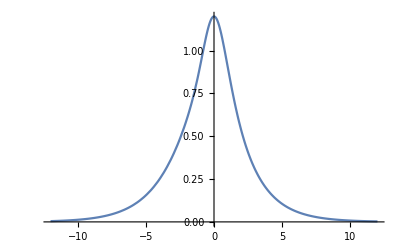

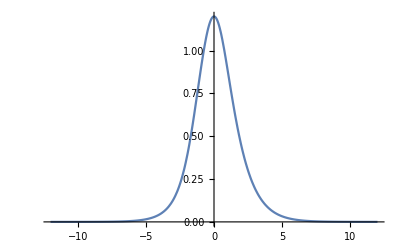

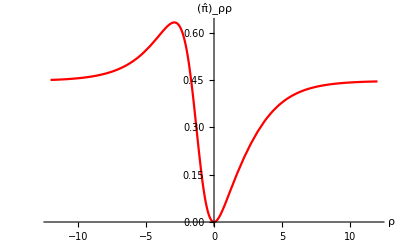

```mathematica
(*μ hat[0] == 1.2*)
Plot[T hat[ρ]/.sols,{ρ,-12,12}]
Plot[μ hat[ρ]/.sols,{ρ,-12,12}]
Plot[π bar ηη[ρ]/.sols,{ρ,-12,12},
PlotStyle->Red,
LabelStyle->{FontSize->18},
AxesLabel->{Style[ρ,FontSize->20,Black],Style[,FontSize->20, Black]}]
```

-Graphics-

-Graphics-

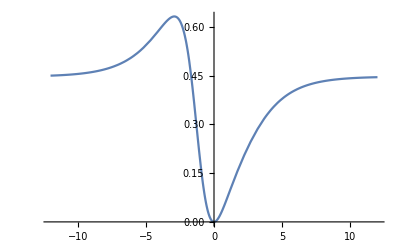

```mathematica
(* μ hat[0] == 0.0*)
Plot[T hat[ρ]/.sols,{ρ,-12,12}]
Plot[μ hat[ρ]/.sols,{ρ,-12,12}]
Plot[π bar ηη[ρ]/.sols,{ρ,-12,12}]
```

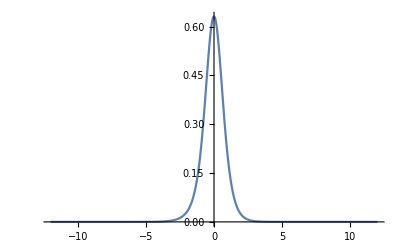

```mathematica
Plot[ℏc (T hat[ρ])^4 Cosh[(μ hat[ρ])/(T hat[ρ])]/.sols,{ρ,-12,12}, PlotRange->Full]
```

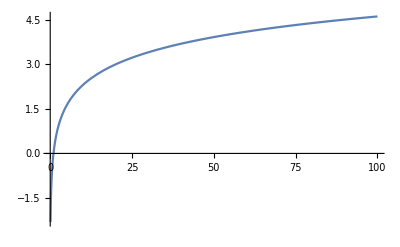

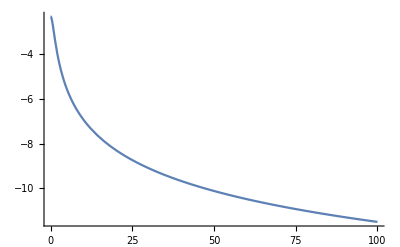

```mathematica
Plot[ArcSinh[-(1-τ^2+r^2)/(2 τ)]/.r->0.0,{τ, 0.1, 100}, PlotRange->All]
Plot[ArcSinh[-(1-τ^2+r^2)/(2 τ)]/.τ->0.1,{r, 0.0, 100}, PlotRange->All]
```

```mathematica
D[(*1/τ^4*)e[ρ[τ]],τ]//FullSimplify
D[1/τ^4 e[ρ[r]],r]//FullSimplify
```

α (T hat[ρ[τ]])^2 (4 Cosh[(μ hat[ρ[τ]])/(T hat[ρ[τ]])] T hat[ρ[τ]] T hat'[ρ[τ]]+Sinh[(μ hat[ρ[τ]])/(T hat[ρ[τ]])] (-μ hat[ρ[τ]] T hat'[ρ[τ]]+T hat[ρ[τ]] μ hat'[ρ[τ]])) ρ'[τ]

1/τ^4 α (T hat[ρ[r]])^2 (4 Cosh[(μ hat[ρ[r]])/(T hat[ρ[r]])] T hat[ρ[r]] T hat'[ρ[r]]+Sinh[(μ hat[ρ[r]])/(T hat[ρ[r]])] (-μ hat[ρ[r]] T hat'[ρ[r]]+T hat[ρ[r]] μ hat'[ρ[r]])) ρ'[r]

```mathematica
D[1/τ^4 ee[ρ[τ]],τ]//FullSimplify
D[1/τ^4 ee[ρ[r]],r]//FullSimplify
```

(-4 ee[ρ[τ]]+τ ee'[ρ[τ]] ρ'[τ])/τ^5

(ee'[ρ[r]] ρ'[r])/τ^4

```mathematica
ArcSinh[-(1-q^2 τ^2+q^2 r^2)/(2q τ)]
D[%,τ]//Simplify[#,Assumptions->{q>0,τ>0}]&
D[%%,r]//Simplify
```

-ArcSinh[(1+q^2 r^2-q^2 τ^2)/(2 q τ)]

(1+q^2 (r^2+τ^2))/(τ √(1+q^4 (r^2-τ^2)^2+2 q^2 (r^2+τ^2)))

-(q r)/(τ √(1+((1+q^2 (r^2-τ^2))^2)/(4 q^2 τ^2)))

```mathematica
D[ArcTan[(2q r)/(1+q^2 τ^2-q^2 r^2)],r]//Simplify
D[ArcTan[(2q r)/(1+q^2 τ^2-q^2 r^2)],τ]//Simplify
Cosh[ArcSinh[-(1-q^2 τ^2+q^2 r^2)/(2q τ)]]//Simplify
Sin[ArcTan[(2q r)/(1-q^2 r^2+q^2 τ^2)]]//Simplify
```

(2 (q+q^3 (r^2+τ^2)))/(1+q^4 (r^2-τ^2)^2+2 q^2 (r^2+τ^2))

-(4 q^3 r τ)/(1+q^4 (r^2-τ^2)^2+2 q^2 (r^2+τ^2))

√(1+((1+q^2 (r^2-τ^2))^2)/(4 q^2 τ^2))

-(2 q r)/((-1+q^2 (r^2-τ^2)) √(1+(4 q^2 r^2)/((-1+q^2 (r^2-τ^2))^2)))

```mathematica
Table[Sinh[ArcTanh[(2τ r)/(1+τ^2+r^2)]]/.τ->τ0,{τ0,1.1, 2.1, 0.1}]
Plot[%,{r, 0, 30}, PlotRange->Full]
```

{(2.2 r)/((2.21+r^2) √(1-(4.84 r^2)/((2.21+r^2)^2))),(2.4 r)/((2.44+r^2) √(1-(5.76 r^2)/((2.44+r^2)^2))),(2.6 r)/((2.69+r^2) √(1-(6.76 r^2)/((2.69+r^2)^2))),(2.8 r)/((2.96+r^2) √(1-(7.84 r^2)/((2.96+r^2)^2))),(3. r)/((3.25+r^2) √(1-(9. r^2)/((3.25+r^2)^2))),(3.2 r)/((3.56+r^2) √(1-(10.24 r^2)/((3.56+r^2)^2))),(3.4 r)/((3.89+r^2) √(1-(11.56 r^2)/((3.89+r^2)^2))),(3.6 r)/((4.24+r^2) √(1-(12.96 r^2)/((4.24+r^2)^2))),(3.8 r)/((4.61+r^2) √(1-(14.44 r^2)/((4.61+r^2)^2))),(4. r)/((5.+r^2) √(1-(16. r^2)/((5.+r^2)^2))),(4.2 r)/((5.41+r^2) √(1-(17.64 r^2)/((5.41+r^2)^2)))}

```mathematica
1/τ^4
```

{1/(√(1-(4.84 r^2)/((2.21+r^2)^2))),1/(√(1-(492.84 r^2)/((124.21+r^2)^2))),1/(√(1-(1780.84 r^2)/((446.21+r^2)^2))),1/(√(1-(3868.84 r^2)/((968.21+r^2)^2))),1/(√(1-(6756.84 r^2)/((1690.21+r^2)^2))),1/(√(1-(10444.8 r^2)/((2612.21+r^2)^2))),1/(√(1-(14932.8 r^2)/((3734.21+r^2)^2))),1/(√(1-(20220.8 r^2)/((5056.21+r^2)^2))),1/(√(1-(26308.8 r^2)/((6578.21+r^2)^2))),1/(√(1-(33196.8 r^2)/((8300.21+r^2)^2)))}

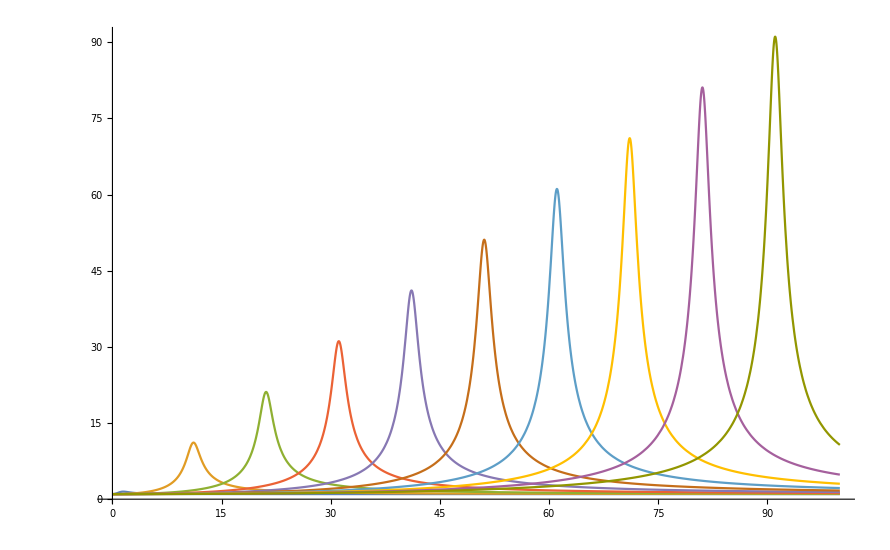

```mathematica
Manipulate[Plot[Cosh[ArcTanh[(2τ r)/(1+τ^2+r^2)]]/.τ->τ0,{r, 0, 100}, PlotRange->Full],{τ0,1.1, 100.1, 10}]
```

## Change of coordinates of solutions

```mathematica
ρ[τ_,r_]:=ArcSinh[-(1-τ^2+r^2)/(2τ)];
T[τ_,r_]:=ℏc((T hat[ρ[τ,r]]/.sols)/τ)[[1]];
μ[τ_,r_]:=ℏc((μ hat[ρ[τ,r]]/.sols)/τ)[[1]];
T[τ_,x_,y_]:= T[τ,√(x^2+y^2)];
μ[τ_,x_,y_]:= μ[τ,√(x^2+y^2)];
u r[τ_,r_]:=Sinh[ArcTanh[(2τ r)/(1+τ^2+r^2)]];
u x[τ_,x_,y_]:=Piecewise[{{x/(√(x^2+y^2))Sinh[ArcTanh[(2τ √(x^2+y^2))/(1+τ^2+x^2+y^2)]],√(x^2+y^2)≠0},{0.0,√(x^2+y^2)==0}}];
u y[τ_,x_,y_]:=Piecewise[{{y/(√(x^2+y^2))Sinh[ArcTanh[(2τ √(x^2+y^2))/(1+τ^2+x^2+y^2)]],√(x^2+y^2)≠0},{0.0,√(x^2+y^2)==0}}];
π hat ηη[τ_,r_]:=(*4/3 α ℏc (((T hat[ρ[τ,r]])^4 Cosh[(μ hat[ρ[τ,r]])/(T hat[ρ[τ,r]])])/.sols[[1]])*)ℏc((e[ρ[τ,r]]+p[ρ[τ,r]])/.sols[[1]])(π bar ηη[ρ[τ,r]]/.sols)[[1]]; 
π ηη[τ_,x_,y_]:=1/τ^6 π hat ηη(*[τ,√(x^2+y^2)]*);
π xx[τ_,x_,y_]:=-1/2 1/τ^4(1+Piecewise[{{(x/(√(x^2+y^2)))^2 Sinh[ArcTanh[(2τ √(x^2+y^2))/(1+τ^2+x^2+y^2)]]^2,x^2+y^2≠0},{0.0,x^2+y^2==0}}])π hat ηη(*[τ,√(x^2+y^2)]*);
π yy[τ_,x_,y_]:=-1/2 1/τ^4(1+Piecewise[{{(y/(√(x^2+y^2)))^2 Sinh[ArcTanh[(2τ √(x^2+y^2))/(1+τ^2+x^2+y^2)]]^2,x^2+y^2≠0},{0.0,x^2+y^2==0}}])π hat ηη(*[τ,√(x^2+y^2)]*);
π xy[τ_,x_,y_]:=Piecewise[{{-1/2 1/τ^4(x y)/(x^2+y^2)Sinh[ArcTanh[(2τ √(x^2+y^2))/(1+τ^2+x^2+y^2)]]^2 π hat ηη[τ,√(x^2+y^2)],x^2+y^2≠0},{0.0,x^2+y^2==0}}];
```

```mathematica
π xx[τ,x,y]
```

-(π hat ηη (1+(Piecewise[{{(4 x^2 τ^2)/((1+x^2+y^2+τ^2)^2 (1-(4 (x^2+y^2) τ^2)/((1+x^2+y^2+τ^2)^2))), x^2+y^2≠0}, {0., x^2+y^2==0}, {0, True}}])))/(2 τ^4)

```mathematica
π xx[τ,x,y]+π yy[τ,x,y]+τ^2 π ηη[τ,x,y]//FullSimplify
```

Piecewise[{{-(2 (x^2+y^2) π hat ηη)/((1+x^2+y^2)^2 τ^2-2 (-1+x^2+y^2) τ^4+τ^6), x^2+y^2≠0}, {0., True}}]

```mathematica
D[ArcTan[(2q r)/(1+q^2 τ^2-q^2 r^2)],r]//Simplify
Sinh[ArcTanh[(1-q^2 τ^2+q^2 r^2)/(2q τ)]]//Simplify
```

(2 (q+q^3 (r^2+τ^2)))/(1+q^4 (r^2-τ^2)^2+2 q^2 (r^2+τ^2))

(1+q^2 (r^2-τ^2))/(2 q τ √(1-((1+q^2 (r^2-τ^2))^2)/(4 q^2 τ^2)))

## Checking GReX output

```mathematica
ρ[τ_,r_]:=ArcSinh[-(1-τ^2+r^2)/(2τ)];
```

```mathematica
ρ[τ,r]/.{τ->1.2,r->35.59702595}
e[%]/.sols
n[%%]/.sols
((e[%%%]+p[%%%])π bar ηη[%%%])/.sols
```

-6.96186

{0.000164953}

{0.0000337758}

{0.00010672}

```mathematica
ρ[τ,r]/.{τ->1.2,r->6.407935688}
e[%]/.sols
n[%%]/.sols
((e[%%%]+p[%%%])π bar ηη[%%%])/.sols
```

-3.52285

{0.133091}

{0.0327291}

{0.109281}

```mathematica
ρ[τ,r]/.{τ->1.2,r->0.9892968549}
e[%] ℏc^4/.sols
n[%%]/.sols
((e[%%%]+p[%%%])π bar ηη[%%%])/.sols
```

-0.222618

{0.0631614}

{8.95761}

{0.407274}

## Plots

### Plot drawing

```mathematica
(* τ's that will be plotted *)
times={1.2,2,3};

plotGrid=GraphicsGrid[
{
{
Plot[Evaluate@Table[T[τ,x,y]/.{τ->times[[i]],y->0},{i,1,Length@times}],{x,-6,6},
PlotRange->{{-6,6},(*{0.04,0.25}*)Automatic},
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","T [GeV]"},PlotTheme->"Monochrome",PlotStyle->Gray,
Axes->False,PlotLabels->Placed[Table[StringJoin[{"τ=",ToString[times[[i]]]," fm"}],{i,1,Length@times}],Table[{Scaled[0.5],Above},{i,1,Length@times}]]],

Plot[Evaluate@Table[μ[τ,x,y]/.{τ->times[[i]],y->0},{i,1,Length@times}],{x,-6,6},
PlotRange->Automatic,
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","μ [GeV]"},PlotTheme->"Monochrome",PlotStyle->Gray,
Axes->False],
Plot[Evaluate@Table[u x[τ,x,y]/.{τ->times[[i]],y->0},{i,1,Length@times}],{x,-6,6},
PlotRange->{{-6,6},{-3,3}},
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","u^x"},PlotTheme->"Monochrome",PlotStyle->Gray,
Axes->False]
},
{
Plot[Evaluate@Table[(τ^2 π ηη[τ,x,y])/.{τ->times[[i]],y->0},{i,1,Length@times}],{x,-6,6},
PlotRange->{{-6,6}, Full},
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","τ^2π^ηη [GeV/fm^3]"},PlotTheme->"Monochrome",PlotStyle->Gray,
Axes->False],
Plot[Evaluate@Table[π yy[τ,x,y]/.{τ->times[[i]],y->0},{i,1,Length@times}],{x,-6,6},
PlotRange->{{-6,6}, Full},
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","π^yy [GeV/fm^3]"},PlotTheme->"Monochrome",PlotStyle->Gray,
Axes->False],

Plot[Evaluate@Table[π xy[τ,x,y]/.{τ->times[[i]],y->x},{i,1,Length@times}],{x,-6,6},
PlotRange->{{-6,6},Full},
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","π^xy [GeV/fm^3]"},PlotTheme->"Monochrome",PlotStyle->Gray,
Axes->False]
}
},ImageSize->128*6];
```

### Display plots

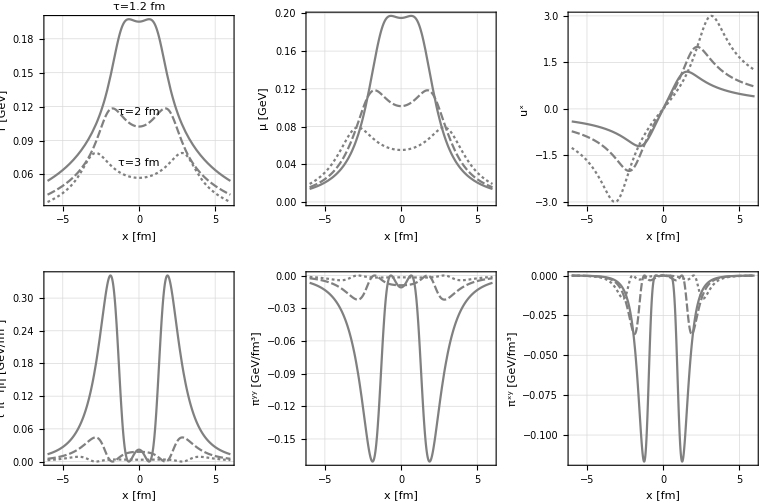

```mathematica
(*μ hat[0] == 1.2, ϕ=0.0*)
plotGrid
```

```mathematica
(*μ hat[0] == 1.2, ϕ≠0.0*)
plotGrid
```

-Graphics-

```mathematica
(*μ hat[0] == 0.0*)
plotGrid
```

-Graphics-

## Output table

### Modules to write output files

```mathematica
(* Table with columns "x [fm], y [fm], T [GeV], u^x, u^y, π^xx [GeV/fm^3], π^yy [GeV/fm^3], π^xy [GeV/fm^3], τ^2π^ηη [GeV/fm^3]" as a function of time τ *)
```

```mathematica
formatted InitialProfile Table[τ_:1,gridMax_:5,gridStep_:0.05,path_:NotebookDirectory[]]:=
Module[
{xMax=Abs@gridMax,
xMin=-Abs@gridMax,
yMax=Abs@gridMax,
yMin=-Abs@gridMax,
Δx=Abs@gridStep,
Δy=Abs@gridStep},
outputTable=ArrayFlatten[
Table[{
DecimalForm@N[x,7],
DecimalForm@N[y,7],
DecimalForm@N[T[Τ,x,y],7],
DecimalForm@N[u x[Τ,x,y],7],
DecimalForm@N[u y[Τ,x,y],7],
DecimalForm@N[π xx[Τ,x,y],7],
DecimalForm@N[π yy[Τ,x,y],7],
DecimalForm@N[π xy[Τ,x,y],7],
DecimalForm@N[(Τ^2 π ηη[Τ,x,y]),7]
}/.{Τ->τ},
{x,xMin,xMax,Δx},{y,yMin,yMax,Δy}],1];
format[x_]:=ToString@NumberForm[x,{7,6},NumberFormat->(StringJoin[{#1,""}/. "":>""/;#2==""]&)];
formattedOutput=Map[format,outputTable,{2}];
filename="Initial_Profile_tau="<>ToString[τ]<>"fm.dat";
completePath=FileNameJoin[{path,filename}];
Export[completePath,formattedOutput,"Table","FieldSeparators"->"     "];
];
formatted yeq0 Table[τ_:1,gridMax_:5,gridStep_:0.05,path_:NotebookDirectory[]]:=
Module[
{xMax=Abs@gridMax,
xMin=-Abs@gridMax,
Δx=Abs@gridStep},
outputTable=ArrayFlatten[
Table[{
DecimalForm@N[x,7],
DecimalForm@N[y,7],
DecimalForm@N[T[Τ,x,y],7],
DecimalForm@N[u x[Τ,x,y],7],
DecimalForm@N[u y[Τ,x,y],7],
DecimalForm@N[π xx[Τ,x,y],7],
DecimalForm@N[π yy[Τ,x,y],7],
DecimalForm@N[π xy[Τ,x,y],7],
DecimalForm@N[(Τ^2 π ηη[Τ,x,y]),7]
}/.{Τ->τ,y->0},
{x,xMin,xMax,Δx}],0];
format[x_]:=ToString@NumberForm[x,{7,6},NumberFormat->(StringJoin[{#1,""}/. "":>""/;#2==""]&)];
formattedOutput=Map[format,outputTable,{2}];
filename="y=0_tau="<>ToString[τ]<>"_SemiAnalytic.dat";
completePath=FileNameJoin[{path,filename}];
Export[completePath,formattedOutput,"Table","FieldSeparators"->"     "];
];
formatted yeqx Table[τ_:1,gridMax_:5,gridStep_:0.05,path_:NotebookDirectory[]]:=
Module[
{xMax=Abs@gridMax,
xMin=-Abs@gridMax,
Δx=Abs@gridStep},
outputTable=ArrayFlatten[
Table[{
DecimalForm@N[x,7],
DecimalForm@N[y,7],
DecimalForm@N[T[Τ,x,y],7],
DecimalForm@N[u x[Τ,x,y],7],
DecimalForm@N[u y[Τ,x,y],7],
DecimalForm@N[π xx[Τ,x,y],7],
DecimalForm@N[π yy[Τ,x,y],7],
DecimalForm@N[π xy[Τ,x,y],7],
DecimalForm@N[(Τ^2 π ηη[Τ,x,y]),7]
}/.{Τ->τ,y->x},
{x,xMin,xMax,Δx}],0];
format[x_]:=ToString@NumberForm[x,{7,6},NumberFormat->(StringJoin[{#1,""}/. "":>""/;#2==""]&)];
formattedOutput=Map[format,outputTable,{2}];
filename="y=x_tau="<>ToString[τ]<>"_SemiAnalytic.dat";
completePath=FileNameJoin[{path,filename}];
Export[completePath,formattedOutput,"Table","FieldSeparators"->"     "];
]
```

### Call module

```mathematica
formatted InitialProfile Table[1,6,0.05]
```

```mathematica
formatted yeq0 Table[1,5,0.05]
```

```mathematica
formatted yeqx Table[2.3,5,0.05]
```

## Output for initial conditions of GReX

```mathematica
Table[{x, e[x]/.sols[[1]], n[x]/.sols[[1]],(((e[x]+p[x])π bar ηη[x])/.sols[[1]])},{x,-20, 20, 0.1}]
Export["/home/ominusliticus/Documents/Research/PostDoc/Code/GReX/Problems/Gubser_Test_Viscous/initial_conditions_viscous.tsv",%]
```

{{-20.,3.44718×10^-16,1.60104×10^-16,2.05572×10^-16},{-19.9,4.24007×10^-16,1.95558×10^-16,2.52857×10^-16},{-19.8,5.2154×10^-16,2.38922×10^-16,3.11022×10^-16},{-19.7,6.41519×10^-16,2.91917×10^-16,3.82575×10^-16},{-19.6,7.89096×10^-16,3.56608×10^-16,4.70587×10^-16},{-19.5,9.70596×10^-16,4.35514×10^-16,5.7883×10^-16},{-19.4,1.19385×10^-15,5.31827×10^-16,7.11977×10^-16},{-19.3,1.46849×10^-15,6.49403×10^-16,8.75768×10^-16},{-19.2,1.80631×10^-15,7.9289×10^-16,1.07724×10^-15},{-19.1,2.22179×10^-15,9.67905×10^-16,1.32504×10^-15},{-19.,2.73284×10^-15,1.18152×10^-15,1.62984×10^-15},{-18.9,3.36152×10^-15,1.44247×10^-15,2.00479×10^-15},{-18.8,4.13488×10^-15,1.7613×10^-15,2.46604×10^-15},{-18.7,5.08605×10^-15,2.15075×10^-15,3.03335×10^-15},{-18.6,6.2558×10^-15,2.62718×10^-15,3.73104×10^-15},{-18.5,7.69463×10^-15,3.21029×10^-15,4.58924×10^-15},{-18.4,9.4646×10^-15,3.92333×10^-15,5.64495×10^-15},{-18.3,1.16418×10^-14,4.79416×10^-15,6.94357×10^-15},{-18.2,1.43195×10^-14,5.85684×10^-15,8.54074×10^-15},{-18.1,1.76129×10^-14,7.15492×10^-15,1.05053×10^-14},{-18.,2.16641×10^-14,8.74042×10^-15,1.29218×10^-14},{-17.9,2.66472×10^-14,1.06758×10^-14,1.58943×10^-14},{-17.8,3.27759×10^-14,1.30355×10^-14,1.95502×10^-14},{-17.7,4.03144×10^-14,1.59148×10^-14,2.40471×10^-14},{-17.6,4.95872×10^-14,1.94327×10^-14,2.95788×10^-14},{-17.5,6.09925×10^-14,2.37334×10^-14,3.63828×10^-14},{-17.4,7.502×10^-14,2.89924×10^-14,4.47513×10^-14},{-17.3,9.22746×10^-14,3.54217×10^-14,5.50452×10^-14},{-17.2,1.13499×10^-13,4.32764×10^-14,6.77076×10^-14},{-17.1,1.39602×10^-13,5.28651×10^-14,8.32816×10^-14},{-17.,1.71708×10^-13,6.4573×10^-14,1.02438×10^-13},{-16.9,2.11201×10^-13,7.88693×10^-14,1.26001×10^-13},{-16.8,2.59776×10^-13,9.63184×10^-14,1.54986×10^-13},{-16.7,3.19519×10^-13,1.17596×10^-13,1.90634×10^-13},{-16.6,3.93002×10^-13,1.43569×10^-13,2.34484×10^-13},{-16.5,4.83391×10^-13,1.75308×10^-13,2.88423×10^-13},{-16.4,5.94561×10^-13,2.1412×10^-13,3.54767×10^-13},{-16.3,7.31291×10^-13,2.61615×10^-13,4.36367×10^-13},{-16.2,8.99474×10^-13,3.19694×10^-13,5.36743×10^-13},{-16.1,1.10634×10^-12,3.90627×10^-13,6.60212×10^-13},{-16.,1.36075×10^-12,4.77166×10^-13,8.12067×10^-13},{-15.9,1.67366×10^-12,5.82792×10^-13,9.98848×10^-13},{-15.8,2.05855×10^-12,7.11774×10^-13,1.22861×10^-12},{-15.7,2.53198×10^-12,8.69265×10^-13,1.51124×10^-12},{-15.6,3.11421×10^-12,1.06146×10^-12,1.85885×10^-12},{-15.5,3.83027×10^-12,1.296×10^-12,2.28638×10^-12},{-15.4,4.71104×10^-12,1.5825×10^-12,2.81229×10^-12},{-15.3,5.7944×10^-12,1.93264×10^-12,3.45922×10^-12},{-15.2,7.12679×10^-12,2.36049×10^-12,4.25492×10^-12},{-15.1,8.76535×10^-12,2.88339×10^-12,5.23354×10^-12},{-15.,1.07807×10^-11,3.52245×10^-12,6.43732×10^-12},{-14.9,1.32597×10^-11,4.30316×10^-12,7.91812×10^-12},{-14.8,1.63085×10^-11,5.25612×10^-12,9.7395×10^-12},{-14.7,2.00577×10^-11,6.41879×10^-12,1.19795×10^-11},{-14.6,2.46689×10^-11,7.83837×10^-12,1.47348×10^-11},{-14.5,3.03406×10^-11,9.57234×10^-12,1.81242×10^-11},{-14.4,3.73162×10^-11,1.16901×10^-11,2.22933×10^-11},{-14.3,4.58942×10^-11,1.42756×10^-11,2.74206×10^-11},{-14.2,5.64437×10^-11,1.7434×10^-11,3.37272×10^-11},{-14.1,6.94189×10^-11,2.12936×10^-11,4.1485×10^-11},{-14.,8.53771×10^-11,2.60092×10^-11,5.10277×10^-11},{-13.9,1.05001×10^-10,3.17682×10^-11,6.27642×10^-11},{-13.8,1.29134×10^-10,3.88048×10^-11,7.71993×10^-11},{-13.7,1.58814×10^-10,4.74039×10^-11,9.4956×10^-11},{-13.6,1.95317×10^-10,5.79094×10^-11,1.16798×10^-10},{-13.5,2.40204×10^-10,7.07347×10^-11,1.43662×10^-10},{-13.4,2.95399×10^-10,8.63913×10^-11,1.76702×10^-10},{-13.3,3.63277×10^-10,1.05517×10^-10,2.17341×10^-10},{-13.2,4.46756×10^-10,1.28885×10^-10,2.67332×10^-10},{-13.1,5.49409×10^-10,1.57427×10^-10,3.2882×10^-10},{-13.,6.7563×10^-10,1.92276×10^-10,4.04442×10^-10},{-12.9,8.30844×10^-10,2.34846×10^-10,4.97458×10^-10},{-12.8,1.02171×10^-9,2.86852×10^-10,6.11871×10^-10},{-12.7,1.2564×10^-9,3.50364×10^-10,7.5259×10^-10},{-12.6,1.54497×10^-9,4.27926×10^-10,9.25665×10^-10},{-12.5,1.89981×10^-9,5.22683×10^-10,1.13855×10^-9},{-12.4,2.33611×10^-9,6.38426×10^-10,1.4004×10^-9},{-12.3,2.87252×10^-9,7.79751×10^-10,1.72244×10^-9},{-12.2,3.53206×10^-9,9.52378×10^-10,2.11855×10^-9},{-12.1,4.343×10^-9,1.16327×10^-9,2.60576×10^-9},{-12.,5.33998×10^-9,1.42083×10^-9,3.20499×10^-9},{-11.9,6.56565×10^-9,1.73536×10^-9,3.94198×10^-9},{-11.8,8.07257×10^-9,2.11962×10^-9,4.84848×10^-9},{-11.7,9.92515×10^-9,2.589×10^-9,5.96343×10^-9},{-11.6,1.22024×10^-8,3.16213×10^-9,7.33464×10^-9},{-11.5,1.50019×10^-8,3.86221×10^-9,9.02116×10^-9},{-11.4,1.84434×10^-8,4.71745×10^-9,1.10956×10^-8},{-11.3,2.26735×10^-8,5.76188×10^-9,1.36468×10^-8},{-11.2,2.78728×10^-8,7.03727×10^-9,1.67844×10^-8},{-11.1,3.42638×10^-8,8.59534×10^-9,2.06435×10^-8},{-11.,4.21189×10^-8,1.04986×10^-8,2.53899×10^-8},{-10.9,5.17725×10^-8,1.28228×10^-8,3.12272×10^-8},{-10.8,6.36369×10^-8,1.56618×10^-8,3.84064×10^-8},{-10.7,7.82173×10^-8,1.91295×10^-8,4.72358×10^-8},{-10.6,9.6134×10^-8,2.33645×10^-8,5.80944×10^-8},{-10.5,1.18151×10^-7,2.85376×10^-8,7.14492×10^-8},{-10.4,1.45203×10^-7,3.4856×10^-8,8.78731×10^-8},{-10.3,1.7844×10^-7,4.25727×10^-8,1.08071×10^-7},{-10.2,2.19277×10^-7,5.1999×10^-8,1.32912×10^-7},{-10.1,2.69444×10^-7,6.35113×10^-8,1.63459×10^-7},{-10.,3.31072×10^-7,7.75719×10^-8,2.01026×10^-7},{-9.9,4.06773×10^-7,9.47475×10^-8,2.47226×10^-7},{-9.8,4.99752×10^-7,1.15723×10^-7,3.04037×10^-7},{-9.7,6.13948×10^-7,1.41344×10^-7,3.73901×10^-7},{-9.6,7.54191×10^-7,1.7264×10^-7,4.59814×10^-7},{-9.5,9.264×10^-7,2.1086×10^-7,5.65456×10^-7},{-9.4,1.13785×10^-6,2.57547×10^-7,6.95364×10^-7},{-9.3,1.39747×10^-6,3.14571×10^-7,8.55104×10^-7},{-9.2,1.71618×10^-6,3.84216×10^-7,1.05152×10^-6},{-9.1,2.1074×10^-6,4.69286×10^-7,1.29304×10^-6},{-9.,2.58756×10^-6,5.73183×10^-7,1.58999×10^-6},{-8.9,3.17685×10^-6,7.00092×10^-7,1.95511×10^-6},{-8.8,3.89995×10^-6,8.55091×10^-7,2.40401×10^-6},{-8.7,4.78715×10^-6,1.04441×10^-6,2.95593×10^-6},{-8.6,5.87556×10^-6,1.27565×10^-6,3.63446×10^-6},{-8.5,7.2106×10^-6,1.55808×10^-6,4.46864×10^-6},{-8.4,8.84796×10^-6,1.90305×10^-6,5.49414×10^-6},{-8.3,0.0000108557,2.32437×10^-6,6.75476×10^-6},{-8.2,0.0000133174,2.83902×10^-6,8.30439×10^-6},{-8.1,0.000016335,3.46756×10^-6,0.0000102092},{-8.,0.0000200335,4.23531×10^-6,0.0000125504},{-7.9,0.0000245656,5.17301×10^-6,0.0000154279},{-7.8,0.0000301182,6.31832×10^-6,0.0000189643},{-7.7,0.0000369197,7.71726×10^-6,0.0000233104},{-7.6,0.0000452492,9.42584×10^-6,0.000028651},{-7.5,0.0000554476,0.0000115128,0.0000352135},{-7.4,0.0000679314,0.0000140617,0.0000432765},{-7.3,0.0000832091,0.0000171751,0.0000531826},{-7.2,0.000101901,0.0000209776,0.000065352},{-7.1,0.000124764,0.0000256222,0.0000803004},{-7.,0.00015272,0.0000312949,0.0000986604},{-6.9,0.000186895,0.0000382238,0.000121209},{-6.8,0.000228657,0.0000466864,0.000148897},{-6.7,0.000279677,0.0000570232,0.000182893},{-6.6,0.000341984,0.0000696479,0.000224627},{-6.5,0.000418049,0.0000850685,0.000275855},{-6.4,0.000510872,0.000103902,0.000338725},{-6.3,0.000624104,0.000126907,0.000415871},{-6.2,0.000762174,0.000155004,0.000510516},{-6.1,0.000930459,0.000189322,0.000626607},{-6.,0.00113548,0.000231238,0.000768973},{-5.9,0.00138514,0.000282434,0.00094352},{-5.8,0.00168901,0.000344965,0.00115747},{-5.7,0.00205868,0.000421339,0.00141964},{-5.6,0.00250814,0.000514623,0.00174082},{-5.5,0.00305435,0.000628557,0.00213415},{-5.4,0.00371772,0.000767716,0.00261569},{-5.3,0.00452294,0.000937683,0.003205},{-5.2,0.00549972,0.00114527,0.0039259},{-5.1,0.00668388,0.00139883,0.0048074},{-5.,0.00811849,0.0017085,0.00588479},{-4.9,0.00985538,0.00208672,0.00720092},{-4.8,0.0119568,0.00254867,0.00880782},{-4.7,0.0144973,0.00311286,0.0107686},{-4.6,0.0175666,0.00380191,0.0131596},{-4.5,0.0212719,0.00464347,0.0160733},{-4.4,0.0257417,0.00567122,0.0196212},{-4.3,0.0311295,0.00692639,0.0239379},{-4.2,0.0376189,0.00845923,0.0291854},{-4.1,0.0454291,0.0103311,0.0355581},{-4.,0.0548218,0.0126169,0.0432893},{-3.9,0.0661091,0.015408,0.0526579},{-3.8,0.0796633,0.018816,0.0639965},{-3.7,0.0959284,0.0229768,0.0777007},{-3.6,0.115434,0.0280564,0.0942392},{-3.5,0.138811,0.0342568,0.114165},{-3.4,0.166814,0.0418245,0.13813},{-3.3,0.200343,0.0510594,0.166892},{-3.2,0.240478,0.0623266,0.201337},{-3.1,0.28851,0.0760699,0.242484},{-3.,0.345993,0.0928288,0.291499},{-2.9,0.4148,0.113257,0.349706},{-2.8,0.497194,0.138148,0.41858},{-2.7,0.595924,0.168459,0.499749},{-2.6,0.714342,0.205348,0.594965},{-2.5,0.856549,0.250204,0.706063},{-2.4,1.02759,0.304696,0.834895},{-2.3,1.2337,0.370816,0.983212},{-2.2,1.4826,0.450926,1.15252},{-2.1,1.78388,0.547816,1.34384},{-2.,2.14949,0.664748,1.55743},{-1.9,2.59425,0.805497,1.7924},{-1.8,3.13652,0.974373,2.04628},{-1.7,3.79888,1.17621,2.31442},{-1.6,4.60874,1.4163,2.58951},{-1.5,5.59881,1.70025,2.86104},{-1.4,6.80713,2.03376,3.11494},{-1.3,8.2763,2.42217,3.3336},{-1.2,10.0514,2.86991,3.4964},{-1.1,12.1761,3.3797,3.58113},{-1.,14.6862,3.95151,3.56636},{-0.9,17.6005,4.58137,3.43485},{-0.8,20.9084,5.26011,3.17788},{-0.7,24.5572,5.97221,2.79967},{-0.6,28.4397,6.69518,2.32079},{-0.5,32.3873,7.39962,1.77919},{-0.4,36.1735,8.05064,1.22739},{-0.3,39.531,8.61045,0.725306},{-0.2,42.1835,9.04238,0.329559},{-0.1,43.8874,9.31546,0.0818823},{0.,44.4753,9.40892,0.},{0.1,43.8874,9.31546,0.0741877},{0.2,42.183,9.04238,0.270728},{0.3,39.5278,8.61045,0.54101},{0.4,36.1613,8.05064,0.833034},{0.5,32.3549,7.39962,1.10169},{0.6,28.3716,6.69518,1.31524},{0.7,24.4361,5.97222,1.45733},{0.8,20.7181,5.26011,1.52527},{0.9,17.3292,4.58137,1.52629},{1.,14.3285,3.95151,1.4733},{1.1,11.7337,3.3797,1.38118},{1.2,9.53235,2.86991,1.26424},{1.3,7.69381,2.42217,1.13467},{1.4,6.17752,2.03376,1.00199},{1.5,4.9396,1.70026,0.873023},{1.6,3.93712,1.4163,0.752237},{1.7,3.13047,1.17621,0.642194},{1.8,2.48466,0.974373,0.544044},{1.9,1.96963,0.805498,0.457945},{2.,1.56009,0.664748,0.383409},{2.1,1.23514,0.547816,0.319568},{2.2,0.977722,0.450926,0.265355},{2.3,0.774006,0.370816,0.219643},{2.4,0.612891,0.304697,0.181322},{2.5,0.48551,0.250204,0.14935},{2.6,0.384801,0.205348,0.122782},{2.7,0.305167,0.16846,0.100777},{2.8,0.242175,0.138148,0.0826027},{2.9,0.192324,0.113257,0.0676266},{3.,0.15285,0.0928288,0.0553103},{3.1,0.121572,0.07607,0.0451984},{3.2,0.0967706,0.0623266,0.036908},{3.3,0.0770897,0.0510594,0.0301192},{3.4,0.0614599,0.0418245,0.0245658},{3.5,0.0490374,0.0342568,0.0200268},{3.6,0.0391558,0.0280563,0.0163198},{3.7,0.0312892,0.0229768,0.0132943},{3.8,0.0250215,0.018816,0.0108264},{3.9,0.0200237,0.015408,0.00881424},{4.,0.0160354,0.0126169,0.00717439},{4.1,0.0128502,0.0103311,0.00583844},{4.2,0.0103044,0.00845923,0.00475042},{4.3,0.00826819,0.0069264,0.00386457},{4.4,0.0066384,0.00567123,0.00314348},{4.5,0.00533299,0.00464346,0.00255664},{4.6,0.00428671,0.00380192,0.00207915},{4.7,0.00344755,0.00311285,0.00169068},{4.8,0.00277411,0.00254867,0.00137469},{4.9,0.00223332,0.00208672,0.00111768},{5.,0.00179882,0.0017085,0.00090867},{5.1,0.0014495,0.00139882,0.000738708},{5.2,0.00116853,0.00114528,0.000600513},{5.3,0.000942411,0.000937682,0.000488152},{5.4,0.00076035,0.000767717,0.000396803},{5.5,0.000613692,0.000628557,0.000322539},{5.6,0.000495501,0.000514622,0.000262169},{5.7,0.000400209,0.00042134,0.000213095},{5.8,0.000323349,0.000344965,0.000173204},{5.9,0.000261331,0.000282435,0.000140779},{6.,0.00021127,0.000231238,0.000114423},{6.1,0.000170848,0.000189323,0.0000930008},{6.2,0.000138196,0.000155004,0.0000755888},{6.3,0.000111814,0.000126907,0.0000614367},{6.4,0.0000904891,0.000103902,0.000049934},{6.5,0.0000732489,0.0000850685,0.0000405851},{6.6,0.000059306,0.000069648,0.0000329865},{6.7,0.0000480272,0.0000570229,0.0000268106},{6.8,0.0000389012,0.0000466867,0.0000217912},{6.9,0.000031515,0.0000382235,0.0000177114},{7.,0.000025536,0.000031295,0.0000143956},{7.1,0.0000206947,0.0000256221,0.0000117006},{7.2,0.000016774,0.0000209776,9.51017×10^-6},{7.3,0.0000135982,0.0000171751,7.72988×10^-6},{7.4,0.0000110252,0.0000140617,6.28285×10^-6},{7.5,8.94033×10^-6,0.0000115128,5.10677×10^-6},{7.6,7.25064×10^-6,9.42586×10^-6,4.15085×10^-6},{7.7,5.88103×10^-6,7.71721×10^-6,3.37389×10^-6},{7.8,4.77071×10^-6,6.31837×10^-6,2.74239×10^-6},{7.9,3.87042×10^-6,5.173×10^-6,2.22909×10^-6},{8.,3.14038×10^-6,4.23532×10^-6,1.81188×10^-6},{8.1,2.54829×10^-6,3.46758×10^-6,1.47277×10^-6},{8.2,2.06803×10^-6,2.839×10^-6,1.19713×10^-6},{8.3,1.67844×10^-6,2.3244×10^-6,9.73095×10^-7},{8.4,1.36235×10^-6,1.90304×10^-6,7.90984×10^-7},{8.5,1.10589×10^-6,1.55808×10^-6,6.42961×10^-7},{8.6,8.97771×10^-7,1.27565×10^-6,5.22641×10^-7},{8.7,7.28872×10^-7,1.04441×10^-6,4.24839×10^-7},{8.8,5.91793×10^-7,8.55098×10^-7,3.45342×10^-7},{8.9,4.80523×10^-7,7.00088×10^-7,2.80721×10^-7},{9.,3.902×10^-7,5.73186×10^-7,2.28194×10^-7},{9.1,3.16874×10^-7,4.69286×10^-7,1.85497×10^-7},{9.2,2.57341×10^-7,3.84216×10^-7,1.50789×10^-7},{9.3,2.09006×10^-7,3.14573×10^-7,1.22576×10^-7},{9.4,1.69756×10^-7,2.57548×10^-7,9.96419×10^-8},{9.5,1.37885×10^-7,2.10863×10^-7,8.09995×10^-8},{9.6,1.12002×10^-7,1.72641×10^-7,6.58452×10^-8},{9.7,9.0982×10^-8,1.41345×10^-7,5.35262×10^-8},{9.8,7.39102×10^-8,1.15725×10^-7,4.35124×10^-8},{9.9,6.00437×10^-8,9.47466×10^-8,3.5372×10^-8},{10.,4.87807×10^-8,7.75721×10^-8,2.87547×10^-8},{10.1,3.96319×10^-8,6.35109×10^-8,2.33754×10^-8},{10.2,3.21999×10^-8,5.19979×10^-8,1.90025×10^-8},{10.3,2.61625×10^-8,4.25727×10^-8,1.54477×10^-8},{10.4,2.12577×10^-8,3.48553×10^-8,1.2558×10^-8},{10.5,1.7273×10^-8,2.85372×10^-8,1.02088×10^-8},{10.6,1.40355×10^-8,2.33643×10^-8,8.29914×10^-9},{10.7,1.14051×10^-8,1.91287×10^-8,6.74668×10^-9},{10.8,9.268×10^-9,1.56614×10^-8,5.48468×10^-9},{10.9,7.53148×10^-9,1.28226×10^-8,4.45875×10^-9},{11.,6.12044×10^-9,1.04981×10^-8,3.62471×10^-9},{11.1,4.9739×10^-9,8.59524×10^-9,2.94672×10^-9},{11.2,4.04221×10^-9,7.03723×10^-9,2.39554×10^-9},{11.3,3.28509×10^-9,5.76154×10^-9,1.94745×10^-9},{11.4,2.66985×10^-9,4.71724×10^-9,1.5832×10^-9},{11.5,2.16986×10^-9,3.86216×10^-9,1.28707×10^-9},{11.6,1.76353×10^-9,3.16203×10^-9,1.04633×10^-9},{11.7,1.43332×10^-9,2.58889×10^-9,8.50626×10^-10},{11.8,1.16495×10^-9,2.1196×10^-9,6.91526×10^-10},{11.9,9.46843×10^-10,1.73536×10^-9,5.62182×10^-10},{12.,7.69585×10^-10,1.42082×10^-9,4.57035×10^-10},{12.1,6.25517×10^-10,1.16327×10^-9,3.71553×10^-10},{12.2,5.08423×10^-10,9.52391×10^-10,3.02059×10^-10},{12.3,4.13256×10^-10,7.79766×10^-10,2.45565×10^-10},{12.4,3.35905×10^-10,6.38415×10^-10,1.99636×10^-10},{12.5,2.73032×10^-10,5.22681×10^-10,1.62297×10^-10},{12.6,2.21933×10^-10,4.27947×10^-10,1.31943×10^-10},{12.7,1.804×10^-10,3.50387×10^-10,1.07267×10^-10},{12.8,1.46638×10^-10,2.86864×10^-10,8.72044×10^-11},{12.9,1.19196×10^-10,2.3486×10^-10,7.08944×10^-11},{13.,9.68916×10^-11,1.92292×10^-10,5.76358×10^-11},{13.1,7.87611×10^-11,1.57435×10^-10,4.68566×10^-11},{13.2,6.40228×10^-11,1.28891×10^-10,3.80929×10^-11},{13.3,5.20432×10^-11,1.05527×10^-10,3.09686×10^-11},{13.4,4.23059×10^-11,8.64005×10^-11,2.5177×10^-11},{13.5,3.43902×10^-11,7.07372×10^-11,2.04683×10^-11},{13.6,2.79557×10^-11,5.79133×10^-11,1.66401×10^-11},{13.7,2.27254×10^-11,4.74165×10^-11,1.35281×10^-11},{13.8,1.84739×10^-11,3.88223×10^-11,1.09982×10^-11},{13.9,1.50175×10^-11,3.17837×10^-11,8.9412×10^-12},{14.,1.2208×10^-11,2.60217×10^-11,7.26899×10^-12},{14.1,9.92422×10^-12,2.13053×10^-11,5.9096×10^-12},{14.2,8.06766×10^-12,1.74431×10^-11,4.8044×10^-12},{14.3,6.55836×10^-12,1.42806×10^-11,3.90585×10^-12},{14.4,5.33151×10^-12,1.1692×10^-11,3.17539×10^-12},{14.5,4.33421×10^-12,9.57288×10^-12,2.58156×10^-12},{14.6,3.5234×10^-12,7.83739×10^-12,2.09874×10^-12},{14.7,2.86426×10^-12,6.41664×10^-12,1.70621×10^-12},{14.8,2.32848×10^-12,5.25393×10^-12,1.38712×10^-12},{14.9,1.89298×10^-12,4.30222×10^-12,1.12774×10^-12},{15.,1.53892×10^-12,3.5226×10^-12,9.16851×10^-13},{15.1,1.25105×10^-12,2.88369×10^-12,7.45374×10^-13},{15.2,1.01702×10^-12,2.36063×10^-12,6.05966×10^-13},{15.3,8.26792×10^-13,1.93256×10^-12,4.92643×10^-13},{15.4,6.72161×10^-13,1.58217×10^-12,4.00521×10^-13},{15.5,5.46444×10^-13,1.29516×10^-12,3.25621×10^-13},{15.6,4.44227×10^-13,1.06007×10^-12,2.6472×10^-13},{15.7,3.61133×10^-13,8.67678×10^-13,2.1521×10^-13},{15.8,2.93589×10^-13,7.10277×10^-13,1.74964×10^-13},{15.9,2.38683×10^-13,5.81477×10^-13,1.42247×10^-13},{16.,1.94042×10^-13,4.76005×10^-13,1.15645×10^-13},{16.1,1.57746×10^-13,3.89664×10^-13,9.40159×10^-14},{16.2,1.28241×10^-13,3.19023×10^-13,7.64328×10^-14},{16.3,1.04257×10^-13,2.61219×10^-13,6.21398×10^-14},{16.4,8.47599×10^-14,2.13888×10^-13,5.05201×10^-14},{16.5,6.8907×10^-14,1.7509×10^-13,4.10721×10^-14},{16.6,5.60181×10^-14,1.43312×10^-13,3.33903×10^-14},{16.7,4.55408×10^-14,1.17304×10^-13,2.71456×10^-14},{16.8,3.70241×10^-14,9.60206×10^-14,2.20694×10^-14},{16.9,3.01003×10^-14,7.85976×10^-14,1.79426×10^-14},{17.,2.44705×10^-14,6.43261×10^-14,1.4587×10^-14},{17.1,1.98935×10^-14,5.2645×10^-14,1.18587×10^-14},{17.2,1.61729×10^-14,4.30895×10^-14,9.64099×10^-15},{17.3,1.31484×10^-14,3.52735×10^-14,7.83817×10^-15},{17.4,1.06896×10^-14,2.88775×10^-14,6.37247×10^-15},{17.5,8.69021×10^-15,2.36424×10^-14,5.18063×10^-15},{17.6,7.06472×10^-15,1.93612×10^-14,4.21165×10^-15},{17.7,5.74345×10^-15,1.586×10^-14,3.42401×10^-15},{17.8,4.66948×10^-15,1.29948×10^-14,2.78378×10^-15},{17.9,3.79645×10^-15,1.0647×10^-14,2.26334×10^-15},{18.,3.08659×10^-15,8.71901×10^-15,1.84015×10^-15},{18.1,2.50927×10^-15,7.13427×10^-15,1.49598×10^-15},{18.2,2.03989×10^-15,5.83556×10^-15,1.21616×10^-15},{18.3,1.65835×10^-15,4.77215×10^-15,9.88698×10^-16},{18.4,1.34823×10^-15,3.90171×10^-15,8.03812×10^-16},{18.5,1.09614×10^-15,3.18914×10^-15,6.5352×10^-16},{18.6,8.91173×10^-16,2.60541×10^-15,5.31323×10^-16},{18.7,7.24485×10^-16,2.12702×10^-15,4.31945×10^-16},{18.8,5.8896×10^-16,1.73591×10^-15,3.51146×10^-16},{18.9,4.78798×10^-16,1.41668×10^-15,2.85468×10^-16},{19.,3.89258×10^-16,1.15645×10^-15,2.32084×10^-16},{19.1,3.16475×10^-16,9.44534×10^-16,1.8869×10^-16},{19.2,2.57299×10^-16,7.72042×10^-16,1.53409×10^-16},{19.3,2.09176×10^-16,6.31663×10^-16,1.24717×10^-16},{19.4,1.70051×10^-16,5.17342×10^-16,1.0139×10^-16},{19.5,1.38246×10^-16,4.23974×10^-16,8.24268×10^-17},{19.6,1.12391×10^-16,3.47396×10^-16,6.70118×10^-17},{19.7,9.13718×10^-17,2.84378×10^-16,5.44795×10^-17},{19.8,7.42842×10^-17,2.32653×10^-16,4.42914×10^-17},{19.9,6.03933×10^-17,1.90287×10^-16,3.60092×10^-17},{20.,4.90998×10^-17,1.55656×10^-16,2.92756×10^-17}}

/home/ominusliticus/Documents/Research/PostDoc/Code/GReX/Problems/Gubser_Test_Viscous/initial_conditions_viscous.tsv

```mathematica
NotebookDirectory[]"test.dat"
```

/home/ominusliticus/Documents/Research/PostDoc/Noronha-Hostler/DissipativeGubserWithMu/ test.dat

```mathematica
Length@Table[x,{x,-12, 12, 0.1}]
```

241

```mathematica
rho
4/3 α ℏc (((T hat[rho])^4 Cosh[(μ hat[rho])/(T hat[rho])]π bar ηη[rho])/.sols[[1]])
format[x_]:=ToString@NumberForm[x,{7,6},NumberFormat->(StringJoin[{#1,""}/. "":>""/;#2==""]&)];
Map[format,(4/3 α ℏc (((T hat[rho])^4 Cosh[(μ hat[rho])/(T hat[rho])]π bar ηη[rho])/.sols[[1]])),0]
```

-12.

4.36244×10^-10

```mathematica
TraditionalForm[4.36243925260463*^-10]
```

4.36244×10^-10

```mathematica
DSolve[{x'[t]+x[t]==-x[t]^2},x[t],t]
```

{{x[t]→-ⅇ^C[1]/(-ⅇ^t+ⅇ^C[1])}}

# Comparing Viscous to Ideal

## Setup

```mathematica
a=1/3;
(*p[ρ_]:=a α (T hat[ρ])^4 Cosh[(μ hat[ρ])/(T hat[ρ])]*)
p[ρ_]:=a α (π^4(T hat[ρ])^4+(μ hat[ρ])^4+2 π^2(μ hat[ρ])^2(T hat[ρ])^2)
e[ρ_]:=1/a p[ρ]
n[ρ_]:=D[p[ρ], μ hat[ρ]]
s[ρ_]:=D[p[ρ], T hat[ρ]]
```

## Ideal system

```mathematica
IdealTmuEvo=Solve[{(1/(e[ρ]+p[ρ])(D[e[ρ],ρ]+2(e[ρ]+p[ρ])Tanh[ρ])//FullSimplify)==0,
(1/(e[ρ]+p[ρ])(D[n[ρ],ρ]+2n[ρ]Tanh[ρ])//FullSimplify)==0},{T hat'[ρ], μ hat'[ρ]}];
IdealConservEqs=(%/.Rule->Equal//FullSimplify)[[1]]

(* Constants for numerical evaluation of PDEs*)
ℏc=(197.326980/1000); 
ηOverS=0.2;
α=3 π^2/90(2(Nc^2-1)+7/2 Nc Nf)/.{Nc->3,Nf->2.5};
c=5;

(* Evaluation of PDEs *)
```

{T hat'[ρ]==-2/3 Tanh[ρ] T hat[ρ],μ hat'[ρ]==-2/3 Tanh[ρ] μ hat[ρ]}

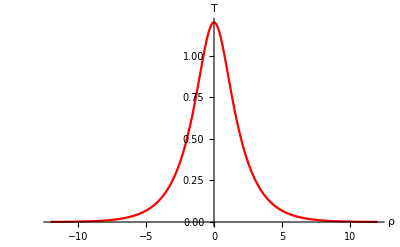

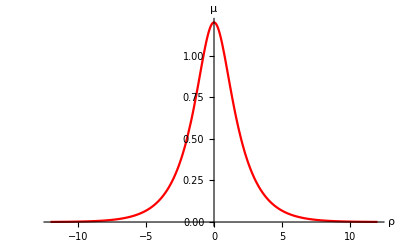

```mathematica
IdealSols=NDSolve[{
IdealConservEqs[[1]],
IdealConservEqs[[2]],
T hat[0]==1.2 (*0.31532/ℏc*),
μ hat[0]==1.2 (*0.162056/ℏc *)},
{T hat,μ hat},
{ρ,-20,20}
];

(*μ hat[0] == 1.2*)
Plot[T hat[ρ]/.IdealSols,{ρ,-12,12},
PlotStyle->Red,
LabelStyle->{FontSize->18},
AxesLabel->{Style[ρ,FontSize->20,Black],Style[,FontSize->20, Black]}]
Plot[μ hat[ρ]/.IdealSols,{ρ,-12,12},
PlotStyle->Red,
LabelStyle->{FontSize->18},
AxesLabel->{Style[ρ,FontSize->20,Black],Style[,FontSize->20, Black]}]

Clear[ℏc,ηOverS,α,c,sols,ρ,T]
```

## Viscous system

{T hat'[ρ]==1/3 Tanh[ρ] T hat[ρ] (-2+π bar ηη[ρ])+(Tanh[ρ] (μ hat[ρ])^2 π bar ηη[ρ])/(π^2 T hat[ρ]),μ hat'[ρ]==-2/3 Tanh[ρ] μ hat[ρ] (1+π bar ηη[ρ])}

-(4 Tanh[ρ])/(3 c)+(4 (π^4 (T hat[ρ])^4+2 π^2 (T hat[ρ])^2 (μ hat[ρ])^2+(μ hat[ρ])^4) π bar ηη[ρ])/(c ηOverS (4 π^4 (T hat[ρ])^3+4 π^2 T hat[ρ] (μ hat[ρ])^2))+4/3 Tanh[ρ] (π bar ηη[ρ])^2+π bar ηη'[ρ]==0

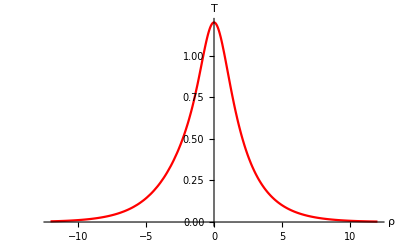

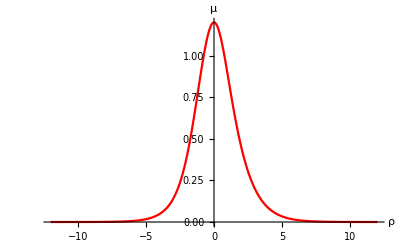

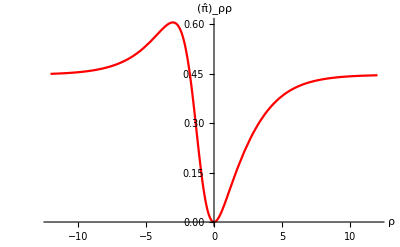

```mathematica
a=1/3;
(*p[ρ_]:=a α (T hat[ρ])^4 Cosh[(μ hat[ρ])/(T hat[ρ])]*)
p[ρ_]:=a α (π^4(T hat[ρ])^4+(μ hat[ρ])^4+2 π^2(μ hat[ρ])^2(T hat[ρ])^2)
e[ρ_]:=1/a p[ρ]
n[ρ_]:=D[p[ρ], μ hat[ρ]]
s[ρ_]:=D[p[ρ], T hat[ρ]]
ViscousTmuEvo=Solve[{(1/(e[ρ]+p[ρ])(D[e[ρ],ρ]+2(e[ρ]+p[ρ])Tanh[ρ]-π bar ηη[ρ](e[ρ]+p[ρ])Tanh[ρ])//FullSimplify)==0,
(1/(e[ρ]+p[ρ])(D[n[ρ],ρ]+2n[ρ]Tanh[ρ])//FullSimplify)==0},{T hat'[ρ], μ hat'[ρ]}];
ViscousConservEqs=(%/.Rule->Equal//FullSimplify)[[1]]
D[π bar ηη[ρ],ρ]+(π bar ηη[ρ])/(e[ρ]+p[ρ])D[e[ρ]+p[ρ],ρ]+1/τR π bar ηη[ρ]-(4/(3c)Tanh[ρ]-8/3 π bar ηη[ρ]Tanh[ρ])-0/(35τR)(π bar ηη[ρ])^2 -0/21 π bar ηη[ρ]Tanh[ρ];
(%/.ViscousTmuEvo)[[1]]//FullSimplify;
ViscousCorrEq=(%/.τR->c ηOverS s[ρ]/(e[ρ]+p[ρ]))==0

(* Constants for numerical evaluation of PDEs*)
ℏc=(197.326980/1000); 
ηOverS=0.2;
α=3 π^2/90(2(Nc^2-1)+7/2 Nc Nf)/.{Nc->3,Nf->2.5};
c=5;

(* Evaluation of PDEs *)
ViscousSols=NDSolve[{
ViscousConservEqs[[1]],
ViscousConservEqs[[2]],
ViscousCorrEq,
T hat[0]==1.2 (*0.31532/ℏc*),
μ hat[0]==1.2 (*0.162056/ℏc *),
π bar ηη[0]==0.0},
{T hat,μ hat,π bar ηη},
{ρ,-20,20}
];

(*μ hat[0] == 1.2*)
Plot[T hat[ρ]/.ViscousSols,{ρ,-12,12},
PlotStyle->Red,
LabelStyle->{FontSize->18},
AxesLabel->{Style[ρ,FontSize->20,Black],Style[,FontSize->20, Black]}]
Plot[μ hat[ρ]/.ViscousSols,{ρ,-12,12},
PlotStyle->Red,
LabelStyle->{FontSize->18},
AxesLabel->{Style[ρ,FontSize->20,Black],Style[,FontSize->20, Black]}]
Plot[π bar ηη[ρ]/.ViscousSols,{ρ,-12,12},
PlotStyle->Red,
LabelStyle->{FontSize->18},
AxesLabel->{Style[ρ,FontSize->20,Black],Style[,FontSize->20, Black]}]

Clear[ℏc,ηOverS,α,c,sols,ρ,T]
```

{T hat'[ρ]==2/3 Tanh[ρ] T hat[ρ] (-1+(2 π bar ηη[ρ])/(1+3 Sech[(μ hat[ρ])/(T hat[ρ])]^2)),μ hat'[ρ]==(2 Tanh[ρ] (μ hat[ρ] (1+3 Sech[(μ hat[ρ])/(T hat[ρ])]^2-2 π bar ηη[ρ])+6 Tanh[(μ hat[ρ])/(T hat[ρ])] T hat[ρ] π bar ηη[ρ]))/(-12+9 Tanh[(μ hat[ρ])/(T hat[ρ])]^2)}

-(4 Tanh[ρ])/(3 c)+(4 α Cosh[(μ hat[ρ])/(T hat[ρ])] (T hat[ρ])^4 π bar ηη[ρ])/(3 c ηOverS (4/3 α Cosh[(μ hat[ρ])/(T hat[ρ])] (T hat[ρ])^3-1/3 α Sinh[(μ hat[ρ])/(T hat[ρ])] (T hat[ρ])^2 μ hat[ρ]))+4/3 Tanh[ρ] (π bar ηη[ρ])^2+π bar ηη'[ρ]==0

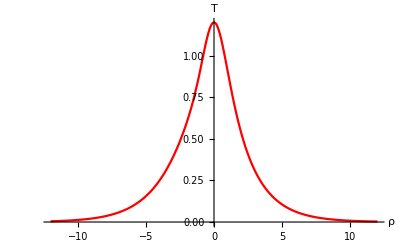

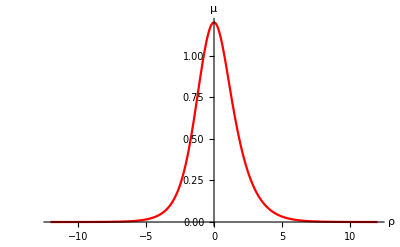

-Graphics-

```mathematica
a=1/3;
p[ρ_]:=a α (T hat[ρ])^4 Cosh[(μ hat[ρ])/(T hat[ρ])]
(*p[ρ_]:=a α (π^4(T hat[ρ])^4+(μ hat[ρ])^4+2 π^2(μ hat[ρ])^2(T hat[ρ])^2)*)
e[ρ_]:=1/a p[ρ]
n[ρ_]:=D[p[ρ], μ hat[ρ]]
s[ρ_]:=D[p[ρ], T hat[ρ]]
ViscousTmuEvo=Solve[{(1/(e[ρ]+p[ρ])(D[e[ρ],ρ]+2(e[ρ]+p[ρ])Tanh[ρ]-π bar ηη[ρ](e[ρ]+p[ρ])Tanh[ρ])//FullSimplify)==0,
(1/(e[ρ]+p[ρ])(D[n[ρ],ρ]+2n[ρ]Tanh[ρ])//FullSimplify)==0},{T hat'[ρ], μ hat'[ρ]}];
ViscousConservEqs=(%/.Rule->Equal//FullSimplify)[[1]]
D[π bar ηη[ρ],ρ]+(π bar ηη[ρ])/(e[ρ]+p[ρ])D[e[ρ]+p[ρ],ρ]+1/τR π bar ηη[ρ]-(4/(3c)Tanh[ρ]-8/3 π bar ηη[ρ]Tanh[ρ])-0/(35τR)(π bar ηη[ρ])^2 -0/21 π bar ηη[ρ]Tanh[ρ];
(%/.ViscousTmuEvo)[[1]]//FullSimplify;
ViscousCorrEq=(%/.τR->c ηOverS s[ρ]/(e[ρ]+p[ρ]))==0

(* Constants for numerical evaluation of PDEs*)
ℏc=(197.326980/1000); 
ηOverS=0.2;
α=3 π^2/90(2(Nc^2-1)+7/2 Nc Nf)/.{Nc->3,Nf->2.5};
c=5;

(* Evaluation of PDEs *)
ViscousSols=NDSolve[{
ViscousConservEqs[[1]],
ViscousConservEqs[[2]],
ViscousCorrEq,
T hat[0]==1.2 (*0.31532/ℏc*),
μ hat[0]==1.2 (*0.162056/ℏc *),
π bar ηη[0]==0.0},
{T hat,μ hat,π bar ηη},
{ρ,-20,20}
];

(*μ hat[0] == 1.2*)
Plot[T hat[ρ]/.ViscousSols,{ρ,-12,12},
PlotStyle->Red,
LabelStyle->{FontSize->18},
AxesLabel->{Style[ρ,FontSize->20,Black],Style[,FontSize->20, Black]}]
Plot[μ hat[ρ]/.ViscousSols,{ρ,-12,12},
PlotStyle->Red,
LabelStyle->{FontSize->18},
AxesLabel->{Style[ρ,FontSize->20,Black],Style[,FontSize->20, Black]}]
Plot[π bar ηη[ρ]/.ViscousSols,{ρ,-12,12},
PlotStyle->Red,
LabelStyle->{FontSize->18},
AxesLabel->{Style[ρ,FontSize->20,Black],Style[,FontSize->20, Black]}]

Clear[ℏc,ηOverS,α,c,sols,ρ,T]
```

## Plotting Module

```mathematica
PlottingModule[SolnSet_,VColor_]:=Module[
{ρ,T,μ,u r,u x,u y,π hat ηη,π ηη,π xx,π yy,π xy,ℏc,αα,times},
ℏc=(197.326980/1000);
αα=3 π^2/90(2(Nc^2-1)+7/2 Nc Nf)/.{Nc->3,Nf->2.5};
ρ[τ_,r_]:=ArcSinh[-(1-τ^2+r^2)/(2τ)];
T[τ_,x_,y_]:=ℏc((T hat[ρ[τ,√(x^2+y^2)]]/.SolnSet)/τ)[[1]];
μ[τ_,x_,y_]:=ℏc((μ hat[ρ[τ,√(x^2+y^2)]]/.SolnSet)/τ)[[1]];
u r[τ_,r_]:=Sinh[ArcTanh[(2τ r)/(1+τ^2+r^2)]];
u x[τ_,x_,y_]:=Piecewise[{{x/(√(x^2+y^2))Sinh[ArcTanh[(2τ √(x^2+y^2))/(1+τ^2+x^2+y^2)]],√(x^2+y^2)≠0},{0.0,√(x^2+y^2)==0}}];
u y[τ_,x_,y_]:=Piecewise[{{y/(√(x^2+y^2))Sinh[ArcTanh[(2τ √(x^2+y^2))/(1+τ^2+x^2+y^2)]],√(x^2+y^2)≠0},{0.0,√(x^2+y^2)==0}}];
π hat ηη[τ_,r_]:=ℏc((e[ρ[τ,r]]+p[ρ[τ,r]])/.SolnSet[[1]])(π bar ηη[ρ[τ,r]]/.SolnSet)[[1]]/.{α->αα}; 
π ηη[τ_,x_,y_]:=1/τ^6 π hat ηη[τ,√(x^2+y^2)];
π xx[τ_,x_,y_]:=-1/2 1/τ^4(1+Piecewise[{{(x/(√(x^2+y^2)))^2 Sinh[ArcTanh[(2τ √(x^2+y^2))/(1+τ^2+x^2+y^2)]]^2,x^2+y^2≠0},{0.0,x^2+y^2==0}}])π hat ηη[τ,√(x^2+y^2)];
π yy[τ_,x_,y_]:=-1/2 1/τ^4(1+Piecewise[{{(y/(√(x^2+y^2)))^2 Sinh[ArcTanh[(2τ √(x^2+y^2))/(1+τ^2+x^2+y^2)]]^2,x^2+y^2≠0},{0.0,x^2+y^2==0}}])π hat ηη[τ,√(x^2+y^2)];
π xy[τ_,x_,y_]:=Piecewise[{{-1/2 1/τ^4(x y)/(x^2+y^2)Sinh[ArcTanh[(2τ √(x^2+y^2))/(1+τ^2+x^2+y^2)]]^2 π hat ηη[τ,√(x^2+y^2)],x^2+y^2≠0},{0.0,x^2+y^2==0}}];
times={1.2,2.2,3.2};
Return[GraphicsGrid[
{
{
Plot[Evaluate@Table[T[τ,x,y]/.{τ->times[[i]],y->0},{i,1,Length@times}],{x,-6,6},
PlotRange->{{-6,6},(*{0.04,0.25}*)Automatic},
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","T [GeV]"},PlotTheme->"Monochrome",PlotStyle->Color,
Axes->False,PlotLabels->Placed[Table[StringJoin[{"τ=",ToString[times[[i]]]," fm"}],{i,1,Length@times}],Table[{Scaled[0.5],Above},{i,1,Length@times}]]],

Plot[Evaluate@Table[μ[τ,x,y]/.{τ->times[[i]],y->0},{i,1,Length@times}],{x,-6,6},
PlotRange->Automatic,
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","μ [GeV]"},PlotTheme->"Monochrome",PlotStyle->Color,
Axes->False],

Plot[Evaluate@Table[u x[τ,x,y]/.{τ->times[[i]],y->0},{i,1,Length@times}],{x,-6,6},
PlotRange->{{-6,6},{-3,3}},
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","u^x"},PlotTheme->"Monochrome",PlotStyle->Color,
Axes->False]
},
{
Plot[Evaluate@Table[(τ^2 π ηη[τ,x,y])/.{τ->times[[i]],y->0},{i,1,Length@times}],{x,-6,6},
PlotRange->{{-6,6}, Full},
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","τ^2π^ηη [GeV/fm^3]"},PlotTheme->"Monochrome",PlotStyle->Color,
Axes->False],

Plot[Evaluate@Table[π yy[τ,x,y]/.{τ->times[[i]],y->0},{i,1,Length@times}],{x,-6,6},
PlotRange->{{-6,6}, Full},
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","π^yy [GeV/fm^3]"},PlotTheme->"Monochrome",PlotStyle->Color,
Axes->False],

Plot[Evaluate@Table[π xy[τ,x,y]/.{τ->times[[i]],y->x},{i,1,Length@times}],{x,-6,6},
PlotRange->{{-6,6},Full},
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","π^xy [GeV/fm^3]"},PlotTheme->"Monochrome",PlotStyle->Color,
Axes->False]
}
},ImageSize->128*6],
Module];
]
```

```mathematica
PlotComparisonModule[IdealSolnSet_,ViscousSolnSet_,Colors_, time_]:=Module[
{ρ,T,μ,u r,u x,u y,π hat ηη,π ηη,π xx,π yy,π xy,ℏc,αα,times},
ℏc=(197.326980/1000);
αα=3 π^2/90(2(Nc^2-1)+7/2 Nc Nf)/.{Nc->3,Nf->2.5};
ρ[τ_,r_]:=ArcSinh[-(1-τ^2+r^2)/(2τ)];
T[τ_,x_,y_]:=ℏc(T hat[ρ[τ,√(x^2+y^2)]])/τ;
μ[τ_,x_,y_]:=ℏc(μ hat[ρ[τ,√(x^2+y^2)]])/τ;
u r[τ_,r_]:=Sinh[ArcTanh[(2τ r)/(1+τ^2+r^2)]];
u x[τ_,x_,y_]:=Piecewise[{{x/(√(x^2+y^2))Sinh[ArcTanh[(2τ √(x^2+y^2))/(1+τ^2+x^2+y^2)]],√(x^2+y^2)≠0},{0.0,√(x^2+y^2)==0}}];
u y[τ_,x_,y_]:=Piecewise[{{y/(√(x^2+y^2))Sinh[ArcTanh[(2τ √(x^2+y^2))/(1+τ^2+x^2+y^2)]],√(x^2+y^2)≠0},{0.0,√(x^2+y^2)==0}}];
π hat ηη[τ_,r_]:=ℏc(e[ρ[τ,r]]+p[ρ[τ,r]])π bar ηη[ρ[τ,r]]/.{α->αα}; 
π ηη[τ_,x_,y_]:=1/τ^6 π hat ηη[τ,√(x^2+y^2)];
π xx[τ_,x_,y_]:=-1/2 1/τ^4(1+Piecewise[{{(x/(√(x^2+y^2)))^2 Sinh[ArcTanh[(2τ √(x^2+y^2))/(1+τ^2+x^2+y^2)]]^2,x^2+y^2≠0},{0.0,x^2+y^2==0}}])π hat ηη[τ,√(x^2+y^2)];
π yy[τ_,x_,y_]:=-1/2 1/τ^4(1+Piecewise[{{(y/(√(x^2+y^2)))^2 Sinh[ArcTanh[(2τ √(x^2+y^2))/(1+τ^2+x^2+y^2)]]^2,x^2+y^2≠0},{0.0,x^2+y^2==0}}])π hat ηη[τ,√(x^2+y^2)];
π xy[τ_,x_,y_]:=Piecewise[{{-1/2 1/τ^4(x y)/(x^2+y^2)Sinh[ArcTanh[(2τ √(x^2+y^2))/(1+τ^2+x^2+y^2)]]^2 π hat ηη[τ,√(x^2+y^2)],x^2+y^2≠0},{0.0,x^2+y^2==0}}];
Return[GraphicsGrid[
{
{
Plot[
{
T[τ,x,y]/.IdealSolnSet[[1]]/.{τ->time,y->0},
T[τ,x,y]/.ViscousSolnSet[[1]]/.{τ->time,y->0}
},{x,-6,6},
PlotRange->{{-6,6},(*{0.04,0.25}*)Automatic},
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","T [GeV]"},PlotTheme->"Monochrome",PlotStyle->Colors,
Axes->False,PlotLabels->Placed[StringJoin[{"τ=",ToString[time]," fm"}],{Scaled[0.5],Below}]],

Plot[
{
μ[τ,x,y]/.IdealSolnSet[[1]]/.{τ->time,y->0},
μ[τ,x,y]/.ViscousSolnSet[[1]]/.{τ->time,y->0}
},{x,-6,6},
PlotRange->Automatic,
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","μ [GeV]"},PlotTheme->"Monochrome",PlotStyle->Colors,
Axes->False],

Plot[
{
u x[τ,x,y]/.IdealSolnSet[[1]]/.{τ->time,y->0},
u x[τ,x,y]/.ViscousSolnSet[[1]]/.{τ->time,y->0}
},{x,-6,6},
PlotRange->{{-6,6},{-3,3}},
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","u^x"},PlotTheme->"Monochrome",PlotStyle->Colors,
Axes->False]
},
{
Plot[{0,(τ^2 π ηη[τ,x,y])/.ViscousSolnSet[[1]]/.{τ->time,y->0}},{x,-6,6},
PlotRange->{{-6,6}, Full},
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","τ^2π^ηη [GeV/fm^3]"},PlotTheme->"Monochrome",PlotStyle->Colors,
Axes->False],

Plot[{0,π yy[τ,x,y]/.ViscousSolnSet[[1]]/.{τ->time,y->0}},{x,-6,6},
PlotRange->{{-6,6}, Full},
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","π^yy [GeV/fm^3]"},PlotTheme->"Monochrome",PlotStyle->Colors,
Axes->False],

Plot[{0,π xy[τ,x,y]/.ViscousSolnSet[[1]]/.{τ->time,y->x}},{x,-6,6},
PlotRange->{{-6,6},Full},
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","π^xy [GeV/fm^3]"},PlotTheme->"Monochrome",PlotStyle->Colors,
Axes->False]
}
},ImageSize->128*6],
Module];
]
```

## Plots for P=T^4 Sinh[μ/T]

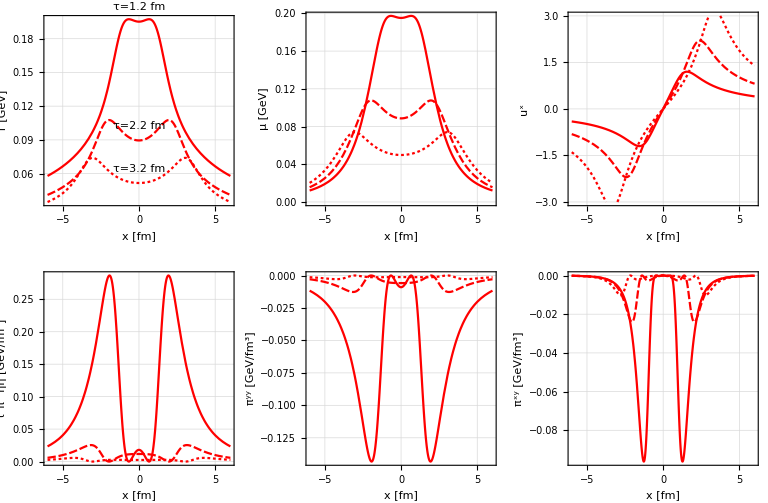

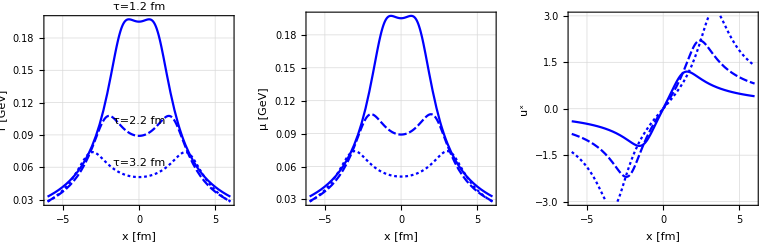

```mathematica
PlottingModule[ViscousSols,Red]
PlottingModule[IdealSols, Blue]
```

```mathematica
s[0]/n[0]/.Ida
```

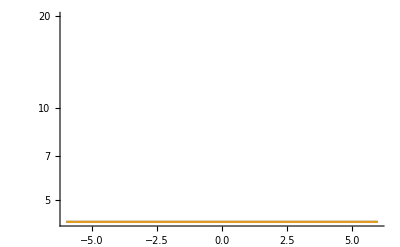

```mathematica
LogPlot[
{s[ArcSinh[-(1-τ^2+r^2)/(2τ)]]/n[ArcSinh[-(1-τ^2+r^2)/(2τ)]]/.IdealSols/.τ->1.2,
s[ArcSinh[-(1-τ^2+r^2)/(2τ)]]/n[ArcSinh[-(1-τ^2+r^2)/(2τ)]]/.IdealSols/.τ->2.2},{r, -6, 6},PlotRange->{0,20}]
```

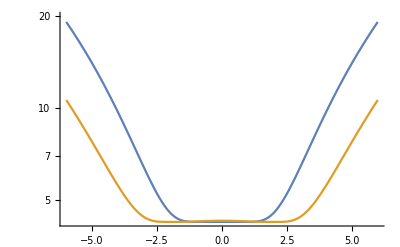

```mathematica
LogPlot[
{s[ArcSinh[-(1-τ^2+r^2)/(2τ)]]/n[ArcSinh[-(1-τ^2+r^2)/(2τ)]]/.ViscousSols/.τ->1.2,
s[ArcSinh[-(1-τ^2+r^2)/(2τ)]]/n[ArcSinh[-(1-τ^2+r^2)/(2τ)]]/.ViscousSols/.τ->2.2},{r, -6, 6},PlotRange->{0,20}]
```

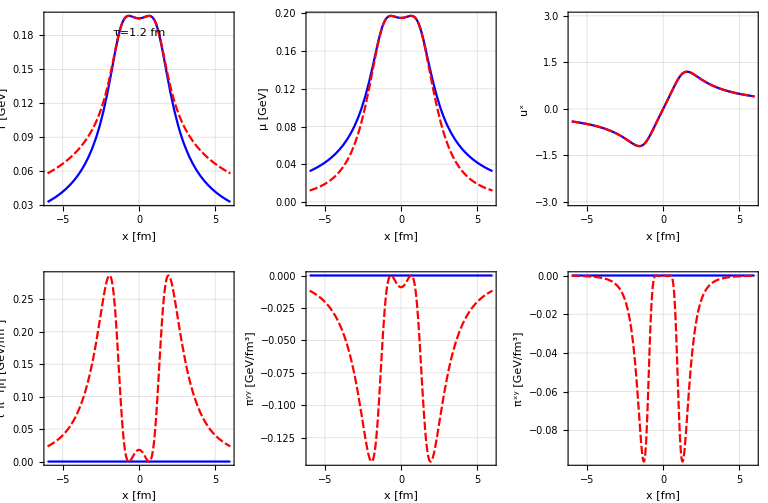

```mathematica
PlotComparisonModule[IdealSols,ViscousSols, {Blue, Red},1.2]
```

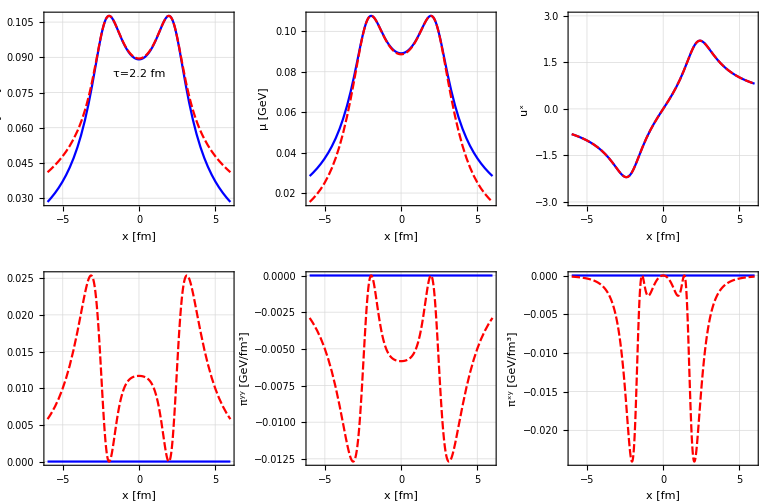

```mathematica
PlotComparisonModule[IdealSols,ViscousSols, {Blue, Red},2.2]
```

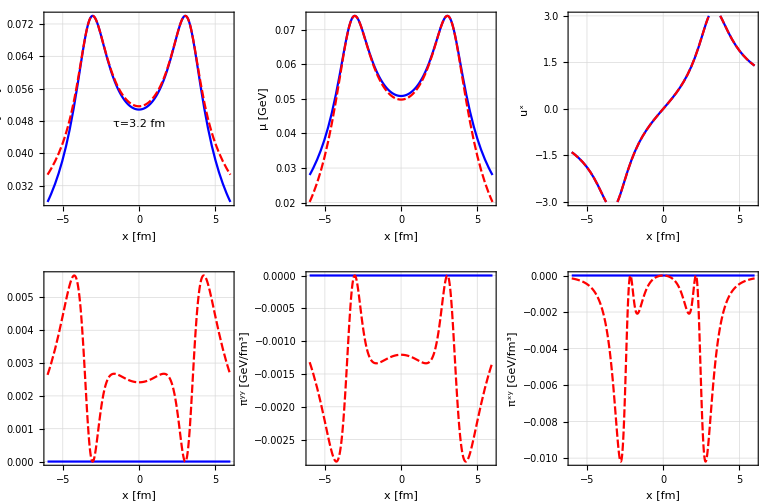

```mathematica
PlotComparisonModule[IdealSols,ViscousSols, {Blue, Red},3.2]
```

## Plots for P=T^4+μ^2+μ^2 T^2

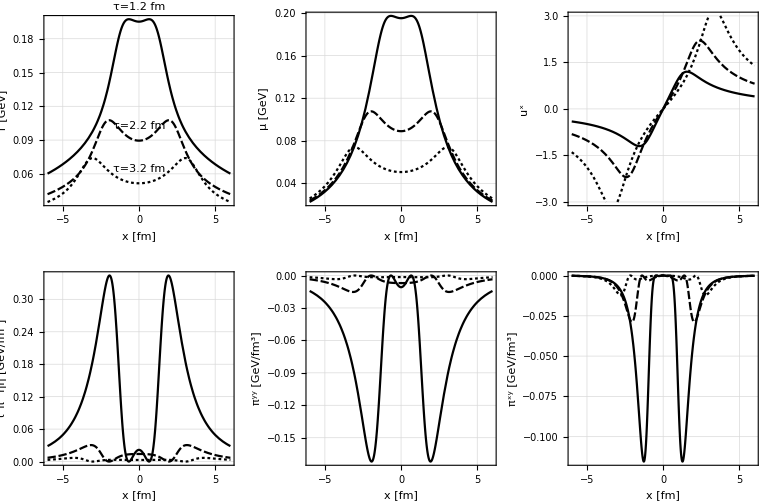

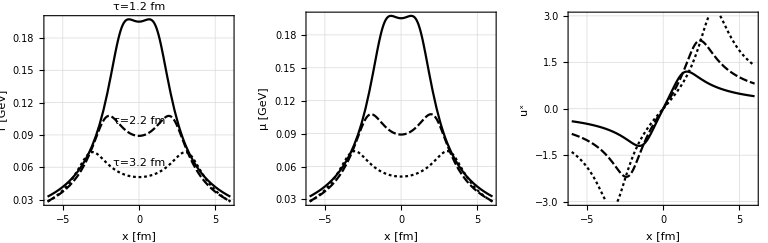

```mathematica
PlottingModule[ViscousSols,Red]
PlottingModule[IdealSols, Blue]
```

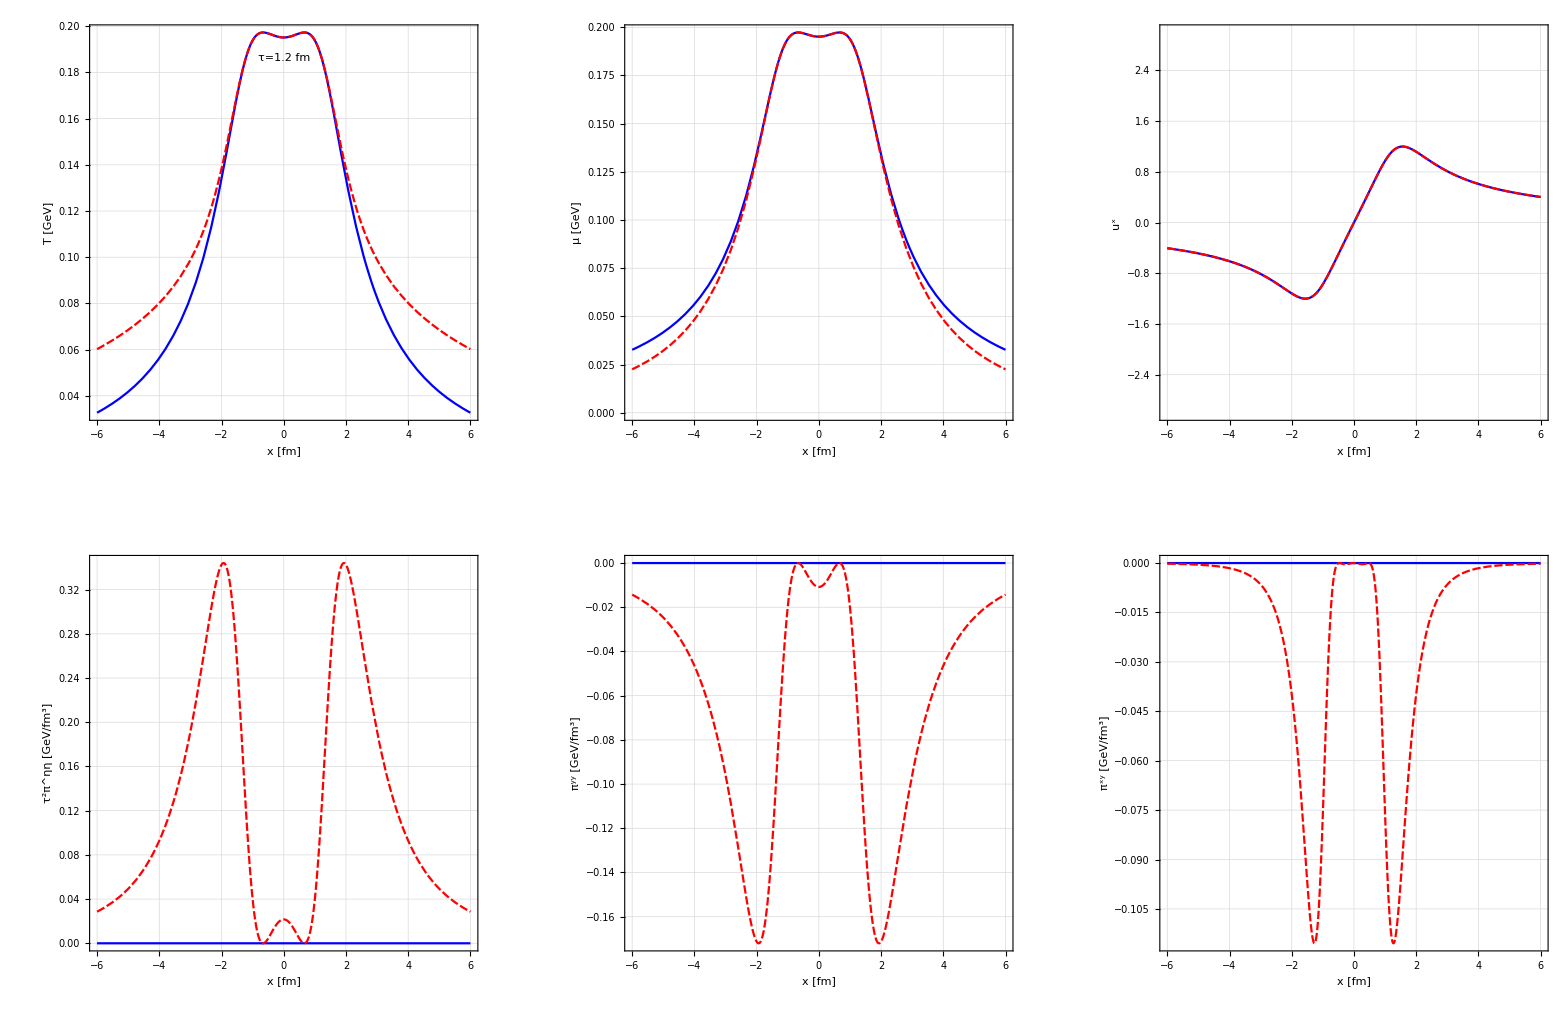

```mathematica
PlotComparisonModule[IdealSols,ViscousSols, {Blue, Red},1.2]
```